# BKM10 Mathematica Notebook:

## A notebook for testing the BKM10 coefficients and code. Written by Dima Watkins [bem8mq@virginia.edu]

Machine precision is set to:

```mathematica
$MachinePrecision
```

15.9546

We are saving plots in:

```mathematica
Directory[]
```

/home/uvaspin

## (#0): Good Mathematica Practice:

```mathematica
ClearAll["Global`*"];
```

## (#1): Static Quantities:

## (#1.1): Physics Quantities:

```mathematica
MassOfProton=Quantity[.93827208816,"Gigaelectronvolts"];
ElectricFormFactorConstant=Quantity[0.710649,"Gigaelectronvolts Squared"];
ElectromagneticFineStructureConstant=1/137.035999177;
ProtonMagneticMoment=2.79284734463;
```

## (#1.2): Lab Settings:

### (#1.2.1): “Standard Kinematics”

```mathematica
k=Quantity[5.75,"Gigaelectronvolts"];
qSquared=Quantity[1.82,"Gigaelectronvolts Squared"];
t=Quantity[-0.17,"Gigaelectronvolts Squared"];
xB=0.34;
```

### (#1.2.2): “Future Kinematics”

```mathematica
kFutureKinematics=Quantity[10.59,"Gigaelectronvolts"];
qSquaredFutureKinematics=Quantity[4.55,"Gigaelectronvolts Squared"];
tFutureKinematics=Quantity[-0.26,"Gigaelectronvolts Squared"];
xBFutureKinematics=0.37;
```

## (#1.3): CFF Settings:

```mathematica
WWOn=True;
WWOff=False;
```

```mathematica
Realℋ=-0.897;
RealℋT=2.444;
Realℰ=-0.541;
RealℰT=2.207;
Imaginaryℋ=2.421;
ImaginaryℋT=1.131;
Imaginaryℰ=0.903;
ImaginaryℰT=5.383;
ℋ=Realℋ+I Imaginaryℋ;
ℋT=RealℋT+I ImaginaryℋT;
ℰ=Realℰ+I Imaginaryℰ;
ℰT=RealℰT+I ImaginaryℰT;
```

## (#1.4): Beam and Target Polarizations:

```mathematica
LeptonλUnpolarizedBeam=0;
LeptonλPlus=1/2;
LeptonλMinus=-1/2;
unpolarizedTargetΛ=0;
lpTargetΛ=1;
```

## (#1.5): Convert from Natural Units:

```mathematica
ConvertGeVMinus6ToNbGevMinus4[ValueInGeVMinus6_]:=Quantity[.389379*1000000*ValueInGeVMinus6,("Nanobarns"*"Gigaelectronvolts"*"Gigaelectronvolts")];
```

## (#2): Derived Quantities:

## (#2.1.1): Derived Kinematics | ϵ

```mathematica
Epsilon[qSquared_,xB_]:=2xB(MassOfProton/(√qSquared));
```

### (#2.1.1.1): ϵ | Standard Kinematic Settings

```mathematica
ϵ=Epsilon[qSquared,xB]
```

0.472936

### (#2.1.1.2): ϵ | Future Kinematic Settings

```mathematica
ϵFutureKinematics=Epsilon[qSquaredFutureKinematics,xBFutureKinematics]
```

0.325503

## (#2.1.2): Derived Kinematics | y

```mathematica
LeptonEnergyFraction[qSquared_,k_,ϵ_]:=(√qSquared)/(ϵ k);
```

### (#2.1.2.1): y | Standard Kinematic Settings

```mathematica
y=LeptonEnergyFraction[qSquared,k,ϵ]
```

0.496096

### (#2.1.2.2): y | Future Kinematic Settings

```mathematica
yFutureKinematics=LeptonEnergyFraction[qSquaredFutureKinematics,kFutureKinematics,ϵFutureKinematics]
```

0.618807

## (#2.1.3): Derived Kinematics | ξ

```mathematica
SkewnessParameter[qSquared_,xB_,t_]:=xB((1+t/(2*qSquared))/(2-xB+(xB t)/qSquared));
```

### (#2.1.3.1): ξ | Standard Kinematic Settings

```mathematica
ξ=SkewnessParameter[qSquared,xB,t]
```

0.199062

### (#2.1.3.2): ξ | Future Kinematic Settings

```mathematica
ξFutureKinematics=SkewnessParameter[qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics]
```

0.223406

## (#2.1.4): Derived Kinematics | t_min

```mathematica
tMinimum[qSquared_,xB_,ϵ_]:=-qSquared*((2(1-xB)(1 - √(1 + ϵ^2)) + ϵ^2)/(4 xB (1-xB)+ ϵ^2));
```

#### (#2.1.4.1): t_min | Standard Kinematic Settings

```mathematica
tMin=tMinimum[qSquared,xB,ϵ]
```

-0.135518 GeV^2

#### (#2.1.4.2): t_min | Future Kinematic Settings:

```mathematica
tMinFutureKinematics=tMinimum[qSquaredFutureKinematics,xBFutureKinematics,ϵFutureKinematics]
```

-0.179145 GeV^2

## (#2.1.5): Derived Kinematics | t'

```mathematica
tPrime[t_,tMinimum_]:=t-tMinimum;
```

#### (#2.1.5.1): t’ | Standard Kinematic Settings

```mathematica
tP=tPrime[t,tMin]
```

-0.0344818 GeV^2

#### (#2.1.5.2): t’ | Future Kinematic Settings

```mathematica
tPFutureKinematics=tPrime[tFutureKinematics,tMinFutureKinematics]
```

-0.0808554 GeV^2

## (#2.1.6): Derived Kinematics | K̃

```mathematica
kTilde[qSquared_,xB_,y_,t_,ϵ_,tMin_]:=√(tMin-t)√((1-xB)√(1+ϵ^2)+((tMin-t)(ϵ^2+4(1-xB)xB))/(4qSquared));
```

#### (#2.1.6.1): K̃ | Standard Kinematic Settings

```mathematica
kT=kTilde[qSquared,xB,y,t,ϵ,tMin]
```

0.159242 GeV

#### (#2.1.6.2): K̃ | Future Kinematic Settings

```mathematica
kTFutureKinematics=kTilde[qSquaredFutureKinematics,xBFutureKinematics,yFutureKinematics,tFutureKinematics,ϵFutureKinematics,tMinFutureKinematics]
```

0.232255 GeV

## (#2.1.7): Derived Kinematics | K

```mathematica
KinematicK[qSquared_,y_,ϵ_,kTilde_]:=kTilde√((1-y+(ϵ^2 y^2)/4)/qSquared);
```

#### (#2.1.7.1): K | Standard Kinematic Settings

```mathematica
K=KinematicK[qSquared,y,ϵ,kT]
```

0.0849269

#### (#2.1.7.2): K | Future Kinematic Settings

```mathematica
KFutureKinematics=KinematicK[qSquaredFutureKinematics,yFutureKinematics,ϵFutureKinematics,kTFutureKinematics]
```

0.0681137

## (#2.2.1): Derived Form Factors | F_E

```mathematica
ElectricFormFactor[t_]:=1/(1-t/ElectricFormFactorConstant)^2;
```

```mathematica
FE=ElectricFormFactor[t]
FEFutureKinematics=ElectricFormFactor[tFutureKinematics]
```

0.651185

0.536026

## (#2.2.2): Derived Form Factors | F_G

```mathematica
MagneticFormFactor[FE_]:=ProtonMagneticMoment*FE;
```

```mathematica
FG=MagneticFormFactor[FE]
FGFutureKinematics=MagneticFormFactor[FEFutureKinematics]
```

1.81866

1.49704

## (#2.2.3): Derived Form Factors | F_2

```mathematica
PauliFormFactor[t_,FElectric_,FMagnetic_]:=(FMagnetic-FElectric)/(1+(-t)/(4 MassOfProton^2));
```

```mathematica
F2=PauliFormFactor[t,FE,FG]
F2FutureKinematics=PauliFormFactor[tFutureKinematics,FEFutureKinematics,FGFutureKinematics]
```

1.11371

0.894936

## (#2.2.4): Derived Form Factors | F_1

```mathematica
DiracFormFactor[t_,FMagnetic_,F2Pauli_]:=FMagnetic-F2Pauli;
```

```mathematica
F1=DiracFormFactor[t,FG,F2]
F1FutureKinematics=DiracFormFactor[tFutureKinematics,FGFutureKinematics,F2FutureKinematics]
```

0.704951

0.602103

## (#2.2.5): Derived Form Factors | ℱ_eff

```mathematica
EffectiveFormFactor[UseWW_,ξ_,ℱ_]:=Module[{},
If[UseWW,
(* The expression for Feff below employs the WW relations !*)
(2 ℱ)/(1+ξ),
(* The expression for Feff below does not use the WW relations!*)
-2ξ ℱ(1/(1+ξ))
]
];
```

## (#3.1): Unpolarized Target:

### (#3.1.1): (C^unp)_(++)(n=0):

```mathematica
CunpPP0[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=-((4(2-y)(1+√(1+ϵ^2)))/(1+ϵ^2)^2)((KTilde^2/qSquared)((2-y)^2/(√(1+ϵ^2)))+(t/qSquared)(1-y-(ϵ^2/4)y^2)(2-xB)(1+(2xB(2-xB+(√(1+ϵ^2)-1)/2+ϵ^2/(2xB))(t/qSquared)+ϵ^2)/((2-xB)(1+√(1+ϵ^2)))));

CunpPP0[qSquared,xB,t,ϵ,y,kT]
```

0.419308

### (#3.1.2): (C^(unp, V))_(++)(n=0):

```mathematica
CunpVPP0[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8(2-y))/(1+ϵ^2)^2)((xB t)/qSquared)(((2-y)^2 KTilde^2)/(√(1+ϵ^2)qSquared)+(1-y-(ϵ^2/4)y^2)((1+√(1+ϵ^2))/2)(1+t/qSquared)(1+((√(1+ϵ^2)-1+2xB)/(1+√(1+ϵ^2)))(t/qSquared)));

CunpVPP0[qSquared,xB,t,ϵ,y,kT]
```

-0.122516

### (#3.1.3): (C^(unp, A))_(++)(n=0):

```mathematica
CunpAPP0[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8(2-y))/(1+ϵ^2)^2)( t/qSquared)((((2-y)^2 KTilde^2)/(√(1+ϵ^2)qSquared))((1+√(1+ϵ^2)-2xB)/2)+(1-y-(ϵ^2/4)y^2)(((1+√(1+ϵ^2))/2)(1+√(1+ϵ^2)-xB+(√(1+ϵ^2)-1+xB(( 3+√(1+ϵ^2)-2xB)/(1+√(1+ϵ^2))))(t/qSquared))-2(KTilde^2/qSquared)));

CunpAPP0[qSquared,xB,t,ϵ,y,kT]
```

-0.66535

### (#3.1.4): (C^unp)_(++)(n=1):

```mathematica
CunpPP1[qSquared_,xB_,t_,ϵ_,y_,K_]:=((-16 K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((1+(1-xB)((√(ϵ^2+1)-1)/(2xB))+ϵ^2/(4xB))((xB t)/qSquared)-(3 ϵ^2)/4)-4K(2-2y+y^2+(ϵ^2/2)y^2)((1+√(1+ϵ^2)-ϵ^2)/(1+ϵ^2)^(5/2))(1-(1-3xB)(t/qSquared)+((1-√(1+ϵ^2)+3 ϵ^2)/(1+√(1+ϵ^2)-ϵ^2))((xB t)/qSquared));

CunpPP1[qSquared,xB,t,ϵ,y,K]
```

-0.405475

### (#3.1.5): (C^(unp, V))_(++)(n=1):

```mathematica
CunpVPP1[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((16K)/(1+ϵ^2)^(5/2))((xB t)/qSquared)((2-y)^2(1-(1-2xB)(t/qSquared))+(1-y-(ϵ^2/4)y^2)((1+√(1+ϵ^2)-2xB)/2)(tPrime/qSquared));
CunpVPP1[qSquared,xB,t,ϵ,y,tP,K]
```

-0.0605142

### (#3.1.6): (C^(unp, A))_(++)(n=1):

```mathematica
CunpAPP1[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((-16K)/(1+ϵ^2)^2)(t/qSquared)((1-y-(ϵ^2/4)y^2)(1-(1-2xB)(t/qSquared)+((4xB(1-xB)+ϵ^2)/(4√(1+ϵ^2)))(tPrime/qSquared))-(2-y)^2(1-xB/2+((1+√(1+ϵ^2)-2xB)/4)(1-t/qSquared)+((4xB(1-xB)+ϵ^2)/(2√(1+ϵ^2)))(tPrime/qSquared)));
CunpAPP1[qSquared,xB,t,ϵ,y,tP,K]
```

-0.189434

### (#3.1.7): (C^unp)_(++)(n=2):

```mathematica
CunpPP2[qSquared_,xB_,t_,ϵ_,y_,tPrime_,KTilde_]:=((8(2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)(((2 ϵ^2)/(√(1+ϵ^2)(1+√(1+ϵ^2))))(KTilde^2/qSquared)+((xB t tPrime)/qSquared^2)(1-xB-(√(1+ϵ^2)-1)/2+ϵ^2/(2xB)));

CunpPP2[qSquared,xB,t,ϵ,y,tP,kT]
```

0.0127529

### (#3.1.8): (C^(unp,V))_(++)(n=2):

```mathematica
CunpVPP2[qSquared_,xB_,t_,ϵ_,y_,tPrime_,KTilde_]:=((8(2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((xB t)/qSquared)((4 KTilde^2)/(√(1+ϵ^2)qSquared)+((1+√(1+ϵ^2)-2xB)/2)(1+t/qSquared)(tPrime/qSquared));
CunpVPP2[qSquared,xB,t,ϵ,y,tP,kT]
```

-0.00476937

### (#3.1.9): (C^(unp,A))_(++)(n=2):

```mathematica
CunpAPP2[qSquared_,xB_,t_,ϵ_,y_,tPrime_,KTilde_]:=((4(2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)( t/qSquared)((4 (1-2xB)KTilde^2)/(√(1+ϵ^2)qSquared)-(3-√(1+ϵ^2)-2xB+ϵ^2/xB)((xB tPrime)/qSquared));
CunpAPP2[qSquared,xB,t,ϵ,y,tP,kT]
```

-0.00518288

### (#3.1.10): (C^unp)_(++)(n=3):

```mathematica
CunpPP3[qSquared_,xB_,t_,ϵ_,y_,K_]:=-8K(1-y-(ϵ^2/4)y^2)((√(1+ϵ^2)-1)/(1+ϵ^2)^(5/2))((1-xB)(t/qSquared)+((√(1+ϵ^2)-1)/2)(1+t/qSquared));

CunpPP3[qSquared,xB,t,ϵ,y,K]
```

0.00028845

### (#3.1.11): (C^(unp, V))_(++)(n=3):

```mathematica
CunpVPP3[qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
CunpVPP3[qSquared,xB,t,ϵ,y,K]
```

-0.000172525

### (#3.1.12): (C^(unp, A))_(++)(n=3):

```mathematica
CunpAPP3[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((16K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((t tPrime)/qSquared^2)(xB(1-xB)+ϵ^2/4);
CunpAPP3[qSquared,xB,t,ϵ,y,tP,K]
```

0.000199468

### (#3.1.13): (C^unp)_(0+)(n=0):

```mathematica
Cunp0P0[qSquared_,xB_,t_,ϵ_,y_,K_]:=((12√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(ϵ^2+((2-6xB-ϵ^2)/3)(t/qSquared));

Cunp0P0[qSquared,xB,t,ϵ,y,K]
```

0.212433

### (#3.1.14): (C^(unp,V))_(0+)(n=0):

```mathematica
Cunp0P0V[qSquared_,xB_,t_,ϵ_,y_,K_]:=((24√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared));

Cunp0P0V[qSquared,xB,t,ϵ,y,K]
```

-0.0599295

### (#3.1.15): (C^(unp,A))_(0+)(n=0):

```mathematica
Cunp0P0A[qSquared_,xB_,t_,ϵ_,y_,K_]:=((4√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))( t/qSquared)(8-6xB+5 ϵ^2)(1-(t/qSquared)((2-12xB(1-xB)-ϵ^2)/(8-6xB+5 ϵ^2)));

Cunp0P0A[qSquared,xB,t,ϵ,y,K]
```

-0.199465

### (#3.1.16): (C^unp)_(0+)(n=1):

```mathematica
Cunp0P1[qSquared_,xB_,t_,ϵ_,y_,tPrime_]:=((8√2√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((2-y)^2(tPrime/qSquared)(1-xB+(((1-xB)xB+ϵ^2/4)/(√(1+ϵ^2)))(tPrime/qSquared))+((1-y-(ϵ^2/4)y^2)/(√(1+ϵ^2)))(1-(1-2xB)(t/qSquared))(ϵ^2-2(1+ϵ^2/(2xB))((xB t)/qSquared)));

Cunp0P1[qSquared,xB,t,ϵ,y,tP]
```

0.595152

### (#3.1.17): (C^(unp,V))_(0+)(n=1):

```mathematica
Cunp0P1V[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((16√2√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)((KTilde^2(2-y)^2)/qSquared+(1-(1-2xB)(t/qSquared))^2(1-y-(ϵ^2/4)y^2));

Cunp0P1V[qSquared,xB,t,ϵ,y,kT]
```

-0.167477

### (#3.1.18): (C^(unp,A))_(0+)(n=1):

```mathematica
Cunp0P1A[qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8√2√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))( t/qSquared)((KTilde^2/qSquared)(1-2xB)(2-y)^2+(1-(1-2xB)(t/qSquared))(1-y-(y^2 ϵ^2)/4)(4-2xB+3 ϵ^2+(t/qSquared)(4xB(1-xB)+ϵ^2)));

Cunp0P1A[qSquared,xB,t,ϵ,y,kT]
```

-0.880759

### (#3.1.19): (C^unp)_(0+)(n=2):

```mathematica
Cunp0P2[qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(1+ϵ^2/2)(1+((1+ϵ^2/(2xB))/(1+ϵ^2/2))((xB t)/qSquared));

Cunp0P2[qSquared,xB,t,ϵ,y,K]
```

-0.65329

### (#3.1.20): (C^(unp,V))_(0+)(n=2):

```mathematica
Cunp0P2V[qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared));

Cunp0P2V[qSquared,xB,t,ϵ,y,K]
```

-0.0199765

### (#3.1.20): (C^(unp,A))_(0+)(n=2):

```mathematica
Cunp0P2A[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((8√2K(2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)( t/qSquared)(1-xB+(tPrime/(2qSquared))((4xB(1-xB)+ϵ^2)/(√(1+ϵ^2))));

Cunp0P2A[qSquared,xB,t,ϵ,y,tP,K]
```

-0.0410451

### (#3.1.21): (S^unp)_(++)(n=1): (Passed!)

```mathematica
SunpPP1[λ_,qSquared_,xB_,ϵ_,y_,tPrime_,K_]:=((8λ K(2-y)y)/(1+ϵ^2))(1+((1-xB+(√(1+ϵ^2)-1)/2)/(1+ϵ^2))(tPrime/qSquared));
SunpPP1[LeptonλPlus,qSquared,xB,ϵ,y,tP,K]
```

0.204836

### (#3.1.22): (S^(unp,V))_(++)(n=1): (Passed!)

```mathematica
SunpPP1V[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8λ K(2-y)y)/(1+ϵ^2)^2)((xB t)/qSquared)(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
SunpPP1V[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

-0.00014525

### (#3.1.23): (S^(unp,A))_(++)(n=1): (Passed!)

```mathematica
SunpPP1A[λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=((8λ K(2-y)y)/(1+ϵ^2))( t/qSquared)(1-(1-2xB)((1+√(1+ϵ^2)-2xB)/(2√(1+ϵ^2)))(tPrime/qSquared));
SunpPP1A[LeptonλPlus,qSquared,xB,t,ϵ,y,tP,K]
```

-0.0194222

### (#3.1.24): (S^unp)_(++)(n=2): (Passed!)

```mathematica
SunpPP2[λ_,qSquared_,xB_,ϵ_,y_,tPrime_]:=-((4λ(1-y-(ϵ^2/4)y^2)y)/(1+ϵ^2)^(3/2))(1+√(1+ϵ^2)-2xB)(tPrime/qSquared)((ϵ^2-xB(√(1+ϵ^2)-1))/(1+√(ϵ^2+1)-2xB)-((2xB+ϵ^2)/(2√(1+ϵ^2)))(tPrime/qSquared));
```

#### (#3.1.24.1): Testing with Kinematic Bin 1:

```mathematica
SunpPP2[LeptonλPlus,qSquared,xB,ϵ,y,tP]
```

0.00135181

#### (#3.1.24.2): Testing with Kinematic Bin 2:

```mathematica
SunpPP2[LeptonλPlus,qSquared,xBFutureKinematics,ϵFutureKinematics,yFutureKinematics,tPFutureKinematics]
```

0.00193443

### (#3.1.25): (S^(unp,V))_(++)(n=2): (Passed!)

```mathematica
SunpPP2V[λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4λ(1-y-(ϵ^2/4)y^2)y)/(1+ϵ^2)^2)((xB t)/qSquared)(1-(1-2xB)(t/qSquared))(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
SunpPP2V[LeptonλPlus,qSquared,xB,t,ϵ,y]
```

-0.000287035

### (#3.1.26): (S^(unp,A))_(++)(n=2): (Passed!)

```mathematica
SunpPP2A[λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_]:=-((8λ (1-y-(ϵ^2/4)y^2)y)/(1+ϵ^2)^2)(( t tPrime)/qSquared^2)(1+√(1+ϵ^2)-2xB)(1+((4(1-xB)xB+ϵ^2)/(4-2xB+3 ϵ^2))(t/qSquared));
SunpPP2A[LeptonλPlus,qSquared,xB,t,ϵ,y,tP]
```

-0.00159642

### (#3.1.27): (S^unp)_(0+)(n=1): (Passed!)

```mathematica
Sunp0P1[λ_,qSquared_,ϵ_,y_,kTilde_]:=((8λ √2(2-y)y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)(kTilde^2/qSquared);
```

```mathematica
Sunp0P1[LeptonλPlus,qSquared,ϵ,y,kT]
```

0.0274939

```mathematica
Sunp0P1[LeptonλPlus,qSquaredFutureKinematics,ϵFutureKinematics,yFutureKinematics,kTFutureKinematics]
```

0.0285462

### (#3.1.28): (S^(unp,V))_(0+)(n=1): (Passed!)

```mathematica
Sunp0P1V[λ_,qSquared_,xB_,t_,ϵ_,y_]:=((4√2λ y (2-y)√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((xB t)/qSquared)(4(1-2xB)(t/qSquared)(1+(xB t)/qSquared)+ϵ^2(1+t/qSquared)^2);
Sunp0P1V[LeptonλPlus,qSquared,xB,t,ϵ,y]
```

-0.00213299

### (#3.1.29): (S^(unp,A))_(0+)(n=1): (Passed!) (MAJOR ERROR WITH UNITS --- DOUBLECHECK!)

```mathematica
Sunp0P1A[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ y (2-y)(1-2xB)√(1-y-(ϵ^2/4)y^2))/(1 +ϵ^2)^2)((t K^2)/qSquared);
Sunp0P1A[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.000425415

### (#3.1.30): (S^unp)_(0+)(n=2) (Passed!):

```mathematica
Sunp0P2[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8λ√2K y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)(1+ϵ^2/2)(1+((1+ϵ^2/(2xB))/(1+ϵ^2/2))((xB t)/qSquared));
```

```mathematica
Sunp0P2[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.119194

```mathematica
Sunp0P2[LeptonλPlus,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϵFutureKinematics,yFutureKinematics,KFutureKinematics]
```

0.122164

### (#3.1.31): (S^(unp,V))_(0+)(n=2) (Passed!):

```mathematica
Sunp0P2V[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ K y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)((xB t)/qSquared)(1-(1-2xB)(t/qSquared));
Sunp0P2V[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.00364475

### (#3.1.32): (S^(unp,A))_(0+)(n=2) (Passed!):

```mathematica
Sunp0P2A[λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((2√2λ K y√(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^2)( t/qSquared)(4-4xB+2 ϵ^2+4(t/qSquared)(4xB(1-xB)+ϵ^2));

Sunp0P2A[LeptonλPlus,qSquared,xB,t,ϵ,y,K]
```

0.00694366

## (#3.2): Longitudinally Polarized Target:

### (#3.2.1): (C^LP)_(++)(n=0):

```mathematica
CLPPP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((-4 λ Λ y(1+√(1+ϵ^2)))/(1+ϵ^2)^(5/2))((2-y)^2(KTilde^2/qSquared)+(1-y+(ϵ^2/4)y^2)((xB t)/qSquared-(1-t/qSquared)(ϵ^2/2))(1+((√(1+ϵ^2)-1+2xB)/(1+√(1+ϵ^2)))(t/qSquared)));
```

```mathematica
CLPPP0[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,kT]
```

0.0573386

### (#3.2.2): (C^(LP,V))_(++)(n=0):

```mathematica
CLPVPP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((4 λ Λ y(1+√(1+ϵ^2)))/(1+ϵ^2)^(5/2))(t/qSquared)((2-y)^2((1+√(1+ϵ^2)-2xB)/(1+√(1+ϵ^2)))(KTilde^2/qSquared)+(1-y-(ϵ^2/4)y^2)(2-xB+(3 ϵ^2)/2)(1+((4(1-xB)xB+ϵ^2)/(4-2xB+3 ϵ^2))(t/qSquared))(1+((√(1+ϵ^2)-1+2xB)/(1+√(1+ϵ^2))) (t/qSquared)));

CLPVPP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.221678

### (#3.2.3): (C^(LP,A))_(++)(n=0):

```mathematica
CLPAPP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((4 λ Λ y)/(1+ϵ^2)^(5/2))((xB t)/qSquared)(2(2-y)^2(KTilde^2/qSquared)+(1-y-(ϵ^2/4)y^2)(1+√(1+ϵ^2))(1-(1-2 xB)(t/qSquared))(1+((√(1+ϵ^2)-1+2 xB)/(1+√(1+ϵ^2)))(t/qSquared)));
```

```mathematica
CLPAPP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.041439

### (#3.2.4): (C^LP)_(++)(n=1):

```mathematica
CLPPP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((4λ Λ K y(2-y))/(1+ϵ^2)^(5/2))(1+√(1+ϵ^2)-ϵ^2)(1-(1-2xB ((2+√(1+ϵ^2))/(1+√(1+ϵ^2)-ϵ^2)))(t/qSquared));
CLPPP1[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.284771

### (#3.2.5): (C^(LP,V))_(++)(n=1):

```mathematica
CLPVPP1[λ_,Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=((8 λ Λ K(2-y)y)/(1+ϵ^2)^2)(√(1+ϵ^2)+2(1-xB))(t/qSquared)(1-((1+(1-ϵ^2)/(√(1+ϵ^2))-2xB(1+(4(1-xB))/(√(1+ϵ^2))))/(2(√(1+ϵ^2)+2(1-xB))))(tPrime/qSquared));
```

```mathematica
CLPVPP1[1.0,1.0,qSquared,xB,t,tP,ϵ,y,K]
```

-0.076538

### (#3.2.6): (C^(LP,A))_(++)(n=1):

```mathematica
CLPAPP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((16λ Λ K (2-y)y)/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared));
CLPAPP1[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0200189

### (#3.2.7): (C^LP)_(++)(n=2):

```mathematica
CLPPP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4λ Λ y(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared-(1-t/qSquared)(ϵ^2/2))(1-√(1+ϵ^2)-(1+√(1+ϵ^2)-2xB)(t/qSquared));
CLPPP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.00244407

### (#3.2.8): (C^(LP,V))_(++)(n=2):

```mathematica
CLPVPP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((2λ Λ y(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(4-2xB+3 ϵ^2)(t/qSquared)(1+((4(1-xB)xB+ϵ^2)/(4-2xB+3 ϵ^2))(t/qSquared))(√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared));
CLPVPP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

-0.00287983

### (#3.2.9): (C^(LP,A))_(++)(n=2):

```mathematica
CLPAPP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=((4λ Λ y(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1-(1-2xB)(t/qSquared))(1-√(1+ϵ^2)-(1+√(1+ϵ^2)-2xB)(t/qSquared));
CLPAPP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

-0.000518959

### (#3.2.10): (C^LP)_(0+)(n=0):

```mathematica
CLP0P0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K (1-xB)y√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(t/qSquared);
CLP0P0[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0137395

### (#3.2.11): (C^(LP,V))_(0+)(n=0):

```mathematica
CLPV0P0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K y√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(t/qSquared)(xB-(t/qSquared)(1-2xB));
CLPV0P0[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.00770017

### (#3.2.12): (C^(LP,A))_(0+)(n=0):

```mathematica
CLPA0P0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ Λ K y√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)((xB t)/qSquared)(1+t/qSquared);
CLPA0P0[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

0.00641681

### (#3.2.13): (C^LP)_(0+)(n=1):

```mathematica
CLP0P1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,KTilde_]:=-((8√2λ Λ K y (1-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(KTilde^2/qSquared);
CLP0P1[1.0,1.0,qSquared,xB,t,ϵ,y,K,kT]
```

-0.00156473

### (#3.2.14): (C^(LP,V))_(0+)(n=1):

```mathematica
CLPV0P1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((8√2λ Λ  y (2-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)((t KTilde^2)/qSquared^2);
CLPV0P1[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.00513622

### (#3.2.15): (C^LP)_(0+)(n=2):

```mathematica
CLP0P2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2λ Λ K y √(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(1+(xB t)/qSquared);
CLP0P2[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.215791

### (#3.2.16): (C^(LP,V))_(0+)(n=2):

```mathematica
CLPV0P2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K y (1-xB)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)( t/qSquared);
CLPV0P2[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0137395

### (#3.2.17): (C^(LP,A))_(0+)(n=2):

```mathematica
CLPA0P2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2λ Λ K y √(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^2)(( xB t)/qSquared)(1+t/qSquared);
CLPA0P2[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.00641681

### (#3.2.10): (C^LP)_(-+)(n=0):

```mathematica
CLPMP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((4 λ Λ y)/(1+ϵ^2)^(5/2))((KTilde^2/qSquared)(2-y)^2(1-√(1+ϵ^2))+(1/2)(1-y-(y^2 ϵ^2)/4)(2 ((xB t)/qSquared)-(1-t/qSquared)ϵ^2)(1-√(1+ϵ^2)-(t/qSquared)(1-2xB+√(1+ϵ^2))));

CLPMP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

-0.00645324

### (#3.2.10): (C^(LP,V))_(-+)(n=0):

```mathematica
CLPVMP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=((2 λ Λ y)/(1+ϵ^2)^(5/2))(t/qSquared)((4-2xB+3 ϵ^2)(1-y-(y^2 ϵ^2)/4)(1+(t/qSquared)((4xB(1-xB)+ϵ^2)/(4-2xB+3 ϵ^2)))(√(1+ϵ^2)-1+(t/qSquared)(1-2xB+√(1+ϵ^2)))+2(2-y)^2(√(1+ϵ^2)-1+2xB)(KTilde^2/qSquared));

CLPVMP0[1.0,1.0,qSquared,xB,t,ϵ,y,kT]
```

0.000107423

### (#3.2.10): (C^(LP,A))_(-+)(n=0):

```mathematica
CLPAMP0[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=((4 λ Λ xB y)/(1+ϵ^2)^(5/2))(t/qSquared)(2(2-y)^2((1-xB)(t/qSquared)(1+(xB t)/qSquared)+(1+t/qSquared)^2(ϵ^2/4))-(1-y-(y^2 ϵ^2)/4)(1-(1-2xB)(t/qSquared))(1-√(1+ϵ^2)-(t/qSquared)(1+√(1+ϵ^2)-2xB)));
CLPAMP0[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.00288225

### (#3.2.10): (C^LP)_(-+)(n=1):

```mathematica
CLPMP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((4 λ Λ K y(2-y))/(1+ϵ^2)^(5/2))(1-ϵ^2-√(1+ϵ^2)-(t/qSquared)(1-ϵ^2-√(1+ϵ^2)-2xB(2-√(1+ϵ^2))));

CLPMP1[1.0,1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0638753

### (#3.2.10): (C^(LP,V))_(-+)(n=1):

```mathematica
CLPVMP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4 λ Λ y(2-y))/(1+ϵ^2)^(5/2))(t/qSquared)(5-4xB+3 ϵ^2-√(1+ϵ^2)-(t/qSquared)(1-ϵ^2-√(1+ϵ^2)-2xB(4-4xB-√(1+ϵ^2))));

CLPVMP1[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.517764

### (#3.2.10): (C^(LP,A))_(-+)(n=1):

```mathematica
CLPAMP1[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((16 λ Λ xB y(2-y))/(1+ϵ^2)^(5/2))(t/qSquared)(1-(1-2xB)(t/qSquared));

CLPAMP1[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.235719

### (#3.2.10): (C^LP)_(-+)(n=2):

```mathematica
CLPMP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((2 λ Λ  y(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(ϵ^2(1+√(1+ϵ^2))-2(t/qSquared)((1-xB)ϵ^2+xB(1+√(1+ϵ^2)))+(t^2/qSquared^2)(2xB+ϵ^2)(1-2xB-√(1+ϵ^2)));

CLPMP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

-0.183867

### (#3.2.10): (C^(LP,V))_(-+)(n=2):

```mathematica
CLPVMP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((2 λ Λ  y(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared)(4-2xB+3 ϵ^2+(t/qSquared)(4xB(1-xB)+ϵ^2))(1+√(1+ϵ^2)-(t/qSquared)(1-√(1+ϵ^2)-2xB));

CLPVMP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.216648

### (#3.2.10): (C^(LP,A))_(-+)(n=2):

```mathematica
CLPAMP2[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4 λ Λ  xB y(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared)(1-(1-2xB)(t/qSquared))(1+√(1+ϵ^2)-(t/qSquared)(1-√(1+ϵ^2)-2xB));

CLPAMP2[1.0,1.0,qSquared,xB,t,ϵ,y]
```

0.0390411

### (#3.2.18): (S^LP)_(++)(n=1):

```mathematica
SLPPP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((4 Λ K (2-2 y + y^2+(ϵ^2/2)y^2))/(1+ϵ^2)^3)(1+√(1+ϵ^2))(2√(1+ϵ^2)-1+((1+√(1+ϵ^2)-2 xB)/(1+√(1+ϵ^2)))(t/qSquared))+((8 K Λ(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)((3 ϵ^2)/2+(1-√(1+ϵ^2)-ϵ^2/2-xB (3-√(1+ϵ^2)))(t/qSquared));
SLPPP1[1.0,qSquared,xB,t,ϵ,y,K]
```

0.650632

### (#3.2.19): (S^(LP,V))_(++)(n=1):

```mathematica
SLPVPP1[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=((8 Λ K (2-2 y + y^2+(ϵ^2/2)y^2))/(1+ϵ^2)^2)(t/qSquared)(1-(((1-2xB)(1+√(1+ϵ^2)-2xB))/(2(1+ϵ^2)))(tPrime/qSquared))+((32 Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(1-((3+√(1+ϵ^2))/4)xB+(5 ϵ^2)/8)(t/qSquared)(1-((1-√(1+ϵ^2)+ϵ^2/2-2xB(3(1-xB)-√(1+ϵ^2)))/(4-xB(√(1+ϵ^2)+3)+(5 ϵ^2)/2))(t/qSquared));
SLPVPP1[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

-0.107266

### (#3.2.20): (S^(LP,A))_(++)(n=1):

```mathematica
SLPAPP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8Λ K (2-2y+y^2+(ϵ^2/2)y^2))/(1+ϵ^2)^3)((xB t)/qSquared) (√(1+ϵ^2)-1+(1+√(1+ϵ^2)-2xB)(t/qSquared))+((8Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(3+√(1+ϵ^2))((xB t)/qSquared)(1-((3-√(1+ϵ^2)-6xB)/(3+√(1+ϵ^2)))(t/qSquared));
```

```mathematica
SLPAPP1[1.0,qSquared,xB,t,ϵ,y,K]
```

-0.0240297

### (#3.2.21): (S^LP)_(++)(n=2):

```mathematica
SLPPP2[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=-((4Λ (2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(((4 KTilde^2)/(√(1+ϵ^2)qSquared))(1+√(1+ϵ^2)-2xB)(1+√(1+ϵ^2)+(xB t)/qSquared)(tPrime/qSquared));
SLPPP2[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

0.00502701

### (#3.2.22): (S^(LP,V))_(++)(n=2):

```mathematica
SLPVPP2[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=((4Λ (2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))(t/qSquared)(((4(1-2xB))/(√(1+ϵ^2)))(KTilde^2/qSquared)-(3-√(1+ϵ^2)-2xB+ϵ^2/xB)((xB tPrime)/qSquared));
SLPVPP2[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

-0.00468532

### (#3.2.23): (S^(LP,A))_(++)(n=2):

```mathematica
SLPAPP2[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=((4Λ (2-y)(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(((4 KTilde^2)/qSquared)-(1+√(1+ϵ^2)-2xB)(1-(((1-2xB)t)/qSquared))(tPrime/qSquared));

SLPAPP2[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

-0.00472387

### (#3.2.24): (S^LP)_(++)(n=3):

```mathematica
SLPPP3[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=-((4Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)((1+√(1+ϵ^2)-2xB)/(1+√(1+ϵ^2)))((ϵ^2 tPrime)/qSquared) ;
SLPPP3[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

0.000260759

### (#3.2.25): (S^(LP,V))_(++)(n=3):

```mathematica
SLPVPP3[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=((4Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(4(1-xB)xB+ϵ^2)((t tPrime)/qSquared^2);
SLPVPP3[1.0,qSquared,xB,t,tP,ϵ,y,K]
```

0.000180319

### (#3.2.26): (S^(LP,A))_(++)(n=3):

```mathematica
SLPAPP3[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_]:=-((8Λ K(1-y-(ϵ^2/4)y^2))/(1+ϵ^2)^3)(1+√(1+ϵ^2)-2xB)((xB t tPrime)/qSquared^2);
SLPAPP3[lpTargetΛ,qSquared,xB,t,tP,ϵ,y,K]

-((8 1  K(1-y-(ϵ^2 y^2/4)))/(1+ϵ^2)^3)
(1+√(1+ϵ^2)-2xB)((xB t tP)/qSquared^2)
```

-0.000155962

-0.181747

0.000858131

### (#3.2.28): (S^LP)_(0+)(n=1):

```mathematica
SLP0P1[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=((8√2Λ√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))((KTilde^2/qSquared)(2-y)^2+(1+t/qSquared)(1-y-(y^2 ϵ^2)/4)(2 ((xB t)/qSquared)-(1-t/qSquared)ϵ^2));
SLP0P1[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

-0.503945

### (#3.2.29): (S^(LP,V))_(0+)(n=1):

```mathematica
SLPV0P1[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,KTilde_]:=-((8√2Λ√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared)((KTilde^2/qSquared)(2-y)^2+(1+t/qSquared)(1-y-(y^2 ϵ^2)/4)(4-2xB+3 ϵ^2+(t/qSquared)(4xB(1-xB)+ϵ^2)));
SLPV0P1[1.0,qSquared,xB,t,tP,ϵ,y,kT]
```

0.785426

### (#3.2.30): (S^(LP,A))_(0+)(n=1):

```mathematica
SLPA0P1[Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((16√2Λ(1-y-(y^2 ϵ^2)/4)^(3/2))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1+t/qSquared)(1-(1-2xB)(t/qSquared));
SLPA0P1[1.0,qSquared,xB,t,ϵ,y]
```

0.139001

### (#3.2.31): (S^LP)_(0+)(n=2):

```mathematica
SLP0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((8√2Λ K(2-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(1+(xB t)/qSquared);
SLP0P2[1.0,qSquared,xB,t,ϵ,y,K]
```

0.591366

### (#3.2.32): (S^(LP,V))_(0+)(n=2):

```mathematica
SLPV0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2Λ K(2-y)(1-xB)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))(t/qSquared);
SLPV0P2[1.0,qSquared,xB,t,ϵ,y,K]
```

0.0376525

### (#3.2.33): (S^(LP,A))_(0+)(n=2):

```mathematica
SLPA0P2[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8√2Λ K (2-y)√(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^(5/2))((xB t)/qSquared)(1+t/qSquared);
SLPA0P2[1.0,qSquared,xB,t,ϵ,y,K]
```

0.017585

### (#3.2.28): (S^LP)_(-+)(n=1):

```mathematica
SLPMP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((4Λ K)/(1+ϵ^2)^3)((2-y)^2(1+2 ϵ^2-√(1+ϵ^2)+(t/qSquared)(1-2xB-√(1+ϵ^2)))-(1-y-(y^2 ϵ^2)/4)(2+ϵ^2-2√(1+ϵ^2)+(t/qSquared)(ϵ^2-4√(1+ϵ^2)+2xB(1+√(1+ϵ^2)))));
SLPMP1[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

-0.149316

### (#3.2.28): (S^(LP,V))_(-+)(n=1):

```mathematica
SLPVMP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((4Λ K)/(1+ϵ^2)^3)(t/qSquared)((2-2y+y^2+(y^2 ϵ^2)/2)(3+2 ϵ^2+√(1+ϵ^2)-2xB(1+√(1+ϵ^2))-(t/qSquared)(1-2xB)(1-2xB-√(1+ϵ^2)))+(1-y-(y^2 ϵ^2)/4)(8+5 ϵ^2-2xB(3-√(1+ϵ^2))-(t/qSquared)(2-ϵ^2+2√(1+ϵ^2)-12xB(1-xB)-4xB√(1+ϵ^2))));
SLPVMP1[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.135048

### (#3.2.28): (S^(LP,A))_(-+)(n=1):

```mathematica
SLPAMP1[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8Λ K(2-2y+y^2+(y^2 ϵ^2)/2))/(1+ϵ^2)^3)(1+√(1+ϵ^2))((xB t)/qSquared)(1-(t/qSquared)((1-√(1+ϵ^2-2xB))/(1+√(1+ϵ^2))))-((8Λ K(1-y+(y^2 ϵ^2)/4))/(1+ϵ^2)^3)((xB t)/qSquared)(3-√(1+ϵ^2)-(t/qSquared)(3+√(1+ϵ^2)-6xB));

SLPAMP1[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.0448748

### (#3.2.28): (S^LP)_(-+)(n=2):

```mathematica
SLPMP2[Λ_,qSquared_,xB_,t_,ϵ_,y_]:=-((4Λ (2-y)(1-y-(y^2 ϵ^2)/4))/(1+ϵ^2)^3)*((t/qSquared)(2+2√(1+ϵ^2)+ϵ^2 √(1+ϵ^2)-xB(3-ϵ^2+3√(1+ϵ^2)))+(t^2/qSquared^2)(ϵ^2-2 xB^2(2+√(1+ϵ^2))+xB(3-ϵ^2+√(1+ϵ^2)))+ϵ^2(1+√(1+ϵ^2)));

SLPMP2[lpTargetΛ,qSquared,xB,t,ϵ,y]
```

-0.410797

### (#3.2.28): (S^(LP,V))_(-+)(n=2):

```mathematica
SLPVMP2[Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=-((4Λ (2-y)√(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^(5/2))(t/qSquared)((2-xB)(1+√(1+ϵ^2))+ϵ^2+(4 KTilde^2(1-2xB))/(qSquared√(1+ϵ^2))+(t/qSquared)(ϵ^2+xB(3-2xB+√(1+ϵ^2))));

SLPVMP2[lpTargetΛ,qSquared,xB,t,ϵ,y,kT]
```

0.867716

### (#3.2.28): (S^(LP,A))_(-+)(n=2):

```mathematica
SLPAMP2[Λ_,qSquared_,xB_,t_,ϵ_,y_,KTilde_]:=-((4Λ (2-y)(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^3)((xB t)/qSquared)(1+4(KTilde^2/qSquared)+√(1+ϵ^2)-2(t/qSquared)(1-2xB-xB√(1+ϵ^2))-(t/qSquared)(1-2xB)(1-2xB-√(1+ϵ^2)));

SLPAMP2[lpTargetΛ,qSquared,xB,t,ϵ,y,kT]
```

0.111615

### (#3.2.28): (S^LP)_(-+)(n=3):

```mathematica
SLPMP3[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=((4Λ K(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^3)(2+ϵ^2+2√(1+ϵ^2)+(t/qSquared)(ϵ^2+2xB(1+√(1+ϵ^2))));

SLPMP3[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.399316

### (#3.2.28): (S^(LP,V))_(-+)(n=3):

```mathematica
SLPVMP3[Λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_]:=-((4Λ K(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^(5/2))(t/qSquared)(4-4xB+(tPrime/qSquared)((4xB(1-xB)+ϵ^2)/(√(1+ϵ^2))));

SLPVMP3[lpTargetΛ,qSquared,xB,t,ϵ,y,tP,K]
```

0.0252566

### (#3.2.28): (S^(LP,A))_(-+)(n=3):

```mathematica
SLPAMP3[Λ_,qSquared_,xB_,t_,ϵ_,y_,K_]:=-((8Λ K(1-y-((y^2 ϵ)/4)^2) )/(1+ϵ^2)^3)((xB t)/qSquared)(1+√(1+ϵ^2)-(t/qSquared)(1-2xB-√(1+ϵ^2)));

SLPAMP3[lpTargetΛ,qSquared,xB,t,ϵ,y,K]
```

0.0120422

## (#3.3): “Curly C” Coefficients:

### (#3.3.1): (𝒞^DVCS)_unp(ℱ): Tested (Failed)

```mathematica
CurlyCDVCSUnp[qSquared_,xB_,t_,ϵ_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:= ((qSquared(qSquared+xB t))/((2-xB)qSquared+xB t)^2)(4(1-xB )ℋ ℋConjugate +4(1-xB+((2qSquared+t)/(qSquared+xB t))(ϵ^2/4))ℋT ℋTConjugate-((xB^2(qSquared+t)^2)/(qSquared(qSquared+xB t)))(ℋ ℰConjugate+ℰ ℋConjugate)-((xB^2 qSquared)/(qSquared+xB t))(ℋT ℰTConjugate+ℰT ℋTConjugate)-((xB^2(qSquared+t)^2)/(qSquared(qSquared+xB t))+(((2-xB)qSquared+xB t)^2/(qSquared(qSquared+xB t)))(t/(4 MassOfProton^2)))ℰ ℰConjugate-((xB^2 qSquared)/(qSquared+xB t))(t/(4 MassOfProton^2))ℰT ℰTConjugate);
```

#### (#3.2.9.1): (𝒞^DVCS)_unp(ℱ | ℱ^*)

```mathematica
CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

13.4781+0. ⅈ

#### (#3.2.9.2): (𝒞^DVCS)_unp(ℱ_eff | ℱ_eff^*)

```mathematica
CurlyCDVCSUnp[qSquared,xB,t,ϵ,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

37.4978+0. ⅈ

#### (#3.2.9.3): (𝒞^DVCS)_unp(ℱ_eff | ℱ^*) | WW On

```mathematica
CurlyCDVCSUnp[qSquared,xB,t,ϵ,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

22.4811+5.60478×10^-16 ⅈ

#### (#3.2.9.3): (𝒞^DVCS)_unp(ℱ_eff | ℱ^*) | WW Off

```mathematica
CurlyCDVCSUnp[qSquared,xB,t,ϵ,EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-4.47513-1.88801×10^-17 ⅈ

### (#3.3.1): (𝒞^DVCS)_LP(ℱ): Tested (Failed)

```mathematica
CurlyCDVCSLP[qSquared_,xB_,t_,ϵ_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=((qSquared(qSquared+xB t))/(√(1+ϵ^2)((2-xB)qSquared+xB t)^2))(4(1-xB+(((3-2xB)qSquared+t)/(qSquared+xB t)) (ϵ^2/4))(ℋ ℋTConjugate+ℋT ℋConjugate)-((qSquared-xB(1-2xB)t)/(qSquared+xB t))xB^2(ℋ ℰTConjugate+ℰT ℋConjugate+ℋT ℰConjugate+ℰ ℋTConjugate)-((4(1-xB)(qSquared+xB t)t+(qSquared+t)^2 ϵ^2)/(2 qSquared(qSquared+xB t)))xB(ℋT ℰConjugate+ℰ ℋTConjugate)-(((2-xB)qSquared+xB t)/(qSquared+xB t))((xB^2(qSquared+t)^2)/(2qSquared((2-xB)qSquared+xB t))+t/(4 MassOfProton^2))xB (ℰ ℰTConjugate+ℰT ℰConjugate));
```

#### (#3.2.9.1): (𝒞^DVCS)_LP(ℱ | ℱ^*)

```mathematica
CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.305289+0. ⅈ

#### (#3.2.9.1): (𝒞^DVCS)_LP(ℱ_eff | ℱ^*)

```mathematica
CurlyCDVCSLP[qSquared,xB,t,ϵ,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.509213-1.84993×10^-15 ⅈ

### (#3.3.1): (𝒞^I)_unp(ℱ): Tested (Failed)

```mathematica
CurlyCInterferenceUnp[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=F1 ℋ-(t/(4 MassOfProton^2))F2 ℰ+(xB/(2-xB+xB (t/qSquared)))(F1+F2)ℋT;

CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]
CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ]]
```

0.266711+2.18475 ⅈ

0.444866+3.64409 ⅈ

### (#3.3.2): (𝒞^(I,V))_unp(ℱ): Tested (Failed)

```mathematica
CurlyCInterferenceVUnp[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℰ_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋ+ℰ);
CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,Realℋ,Realℰ]
```

-0.546098

### (#3.3.3): (𝒞^(I,A))_unp(ℱ): Tested (Failed)

```mathematica
CurlyCInterferenceAUnp[qSquared_,xB_,t_,F1_,F2_,ℋT_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)ℋT;
CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,RealℋT]
```

0.928139

### (#3.3.4): (𝒞^I)_LP(ℱ): Tested (Failed)

```mathematica
CurlyCILP[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋ+(xB/2)(1-t/qSquared)ℰ)+(1+(MassOfProton^2/qSquared)(xB^2/(2-xB+xB (t/qSquared)))(3+t/qSquared))F1 ℋT-(t/qSquared)((2xB(1-2xB))/(2-xB+xB (t/qSquared)))F2 ℋT-(xB/(2-xB+xB (t/qSquared)))((xB/2)(1-t/qSquared)F1+(t/(4 MassOfProton^2))F2)ℰT;
```

#### (#3.3.4.1): This number should always be the same for fixed kinematics:

```mathematica
CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]
CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT]]
```

1.51441+1.7889 ⅈ

2.52599+2.98383 ⅈ

### (#3.3.5): (𝒞^(I,V))_LP(ℱ): Tested (Failed)

```mathematica
CurlyCIVLP[qSquared_,xB_,t_,F1_,F2_,ℋ_,ℰ_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋ+(xB/2)(1-t/qSquared)ℰ);
```

#### (#3.3.5.1): This number should always be the same for fixed kinematics:

```mathematica
CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]
CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℰ]]
```

-0.378836+0.983147 ⅈ

-0.631887+1.63986 ⅈ

### (#3.3.6): (𝒞^(I,A))_LP(ℱ): Tested (Passed!)

```mathematica
CurlyCIALP[qSquared_,xB_,t_,F1_,F2_,ℋT_,ℰT_]:=(xB/(2-xB+xB (t/qSquared)))(F1+F2)(ℋT+2xB (MassOfProton^2/qSquared)ℋT+(xB/2)ℰT);
```

#### (#3.3.6.1): This number should always be the same for fixed kinematics:

```mathematica
CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT]
CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰT]]
```

1.37591+0.918312 ⅈ

2.29498+1.53172 ⅈ

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 0|ℱ):

```mathematica
CurlyCInterferencePlusPlusN0Unp[qSquared_,xB_,t_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP0[qSquared,xB,t,ϵ,y,KTilde]/CunpPP0[qSquared,xB,t,ϵ,y,KTilde])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP0[qSquared,xB,t,ϵ,y,KTilde]/CunpPP0[qSquared,xB,t,ϵ,y,KTilde])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN0Unp[qSquared,xB,t,ϵ,y,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

-1.04648+1.13437 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 0|ℱ_eff):

```mathematica
CurlyCInterferenceZeroPlusN0Unp[WWSetting_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Cunp0P0V[qSquared,xB,t,ϵ,y,K]/Cunp0P0[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Cunp0P0A[qSquared,xB,t,ϵ,y,K]/Cunp0P0[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT]]);

CurlyCInterferenceZeroPlusN0Unp[WWOn,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

-0.0755985+0.239075 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =0|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 1|ℱ):

```mathematica
CurlyCInterferencePlusPlusN1Unp[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP1[qSquared,xB,t,ϵ,y,tPrime,K]/CunpPP1[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP1[qSquared,xB,t,ϵ,y,tPrime,K]/CunpPP1[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN1Unp[qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.618827+2.5738 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 1|ℱ_eff):

```mathematica
CurlyCInterferenceZeroPlusN1Unp[WWSetting_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Cunp0P1V[qSquared,xB,t,ϵ,y,KTilde]/Cunp0P1[qSquared,xB,t,ϵ,y,tPrime])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Cunp0P1A[qSquared,xB,t,ϵ,y,KTilde]/Cunp0P1[qSquared,xB,t,ϵ,y,tPrime])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT]]);

CurlyCInterferenceZeroPlusN1Unp[WWOn,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

-0.159875+0.200255 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =1|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 2|ℱ):

```mathematica
CurlyCInterferencePlusPlusN2Unp[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde]/CunpPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde]/CunpPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN2Unp[qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.0937402+1.5381 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 2|ℱ_eff):

```mathematica
CurlyCInterferenceZeroPlusN2Unp[WWSetting_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Cunp0P2V[qSquared,xB,t,ϵ,y,K]/Cunp0P2[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Cunp0P2A[qSquared,xB,t,ϵ,y,tPrime,K]/Cunp0P2[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT]]);

CurlyCInterferenceZeroPlusN2Unp[WWOn,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.0517161+0.377453 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =2|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_unp(n = 3|ℱ):

```mathematica
CurlyCInterferencePlusPlusN3Unp[qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(CunpVPP3[qSquared,xB,t,ϵ,y,K]/CunpPP3[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CunpAPP3[qSquared,xB,t,ϵ,y,tPrime,K]/CunpPP3[qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];

CurlyCInterferencePlusPlusN3Unp[qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

1.23516+1.72675 ⅈ

### (#3.2.9): ((𝒞^I)_(0+))_unp(n = 3|ℱ_eff):

Note that there are NO C-zero-plus coefficients for the n = 3 mode! That is why we are multiplying by 0 here;:

```mathematica
CurlyCInterferenceZeroPlusN3Unp[WWSetting_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ]]+0*CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+0*CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT]]);

CurlyCInterferenceZeroPlusN3Unp[WWOn,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.044736+0.366452 ⅈ

### (#3.2.9): ((𝒞^I)_(-+))_unp(n =3|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_LP(n = 0|ℱ) Tested (Failed):

```mathematica
CurlyCIPlusPlusN0LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(CLPVPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]/CLPPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CLPAPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]/CLPPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];
CurlyCIPlusPlusN0LP[1,1,qSquared,xB,t,ϵ,y,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.74953

### (#3.2.9): ((𝒞^I)_(0+))_LP(n = 0|ℱ_eff): Tested (Failed):

```mathematica
CurlyCIZeroPlusN0LP[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT]]+(CLPV0P0[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P0[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(CLPA0P0[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P0[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰT]]);

CurlyCIZeroPlusN0LP[WWOn,1,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

0.110619

### (#3.2.9): ((𝒞^I)_(-+))_LP(n =0|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_LP(n = 1|ℱ): Tested (Failed)

```mathematica
CurlyCIPlusPlusN1LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(CLPVPP1[λ,Λ,qSquared,xB,t,tPrime,ϵ,y,K]/CLPPP1[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CLPAPP1[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLPPP1[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlyCIPlusPlusN1LP[1,1,qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.50931

### (#3.2.9): ((𝒞^I)_(0+))_LP(n = 1|ℱ_eff): Tested (Failed)

Note here that (C_(++))^A(n=1) does not exist! That is why we have set it equal to 0!

```mathematica
CurlyCIZeroPlusN1LP[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT]]+(CLPV0P1[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]/CLP0P1[λ,Λ,qSquared,xB,t,ϵ,y,K,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(0/CLP0P1[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰT]]);

CurlyCIZeroPlusN1LP[WWOn,1,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

0.0454352

### (#3.2.9): ((𝒞^I)_(-+))_LP(n =1|ℱ_T):

### (#3.2.9): ((𝒞^I)_(++))_LP(n = 2|ℱ):

```mathematica
CurlyCIPlusPlusN2LP[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(CLPVPP2[λ,Λ,qSquared,xB,t,ϵ,y]/CLPPP2[λ,Λ,qSquared,xB,t,ϵ,y])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(CLPAPP2[λ,Λ,qSquared,xB,t,ϵ,y]/CLPPP2[λ,Λ,qSquared,xB,t,ϵ,y])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];
CurlyCIPlusPlusN2LP[1,1,qSquared,xB,t,ϵ,y,tP,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

1.66863

### (#3.2.9): ((𝒞^I)_(0+))_LP(n = 2|ℱ_eff): Tested (Failed)

```mathematica
CurlyCIZeroPlusN2LP[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT]]+(CLPV0P2[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P2[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(CLPV0P2[λ,Λ,qSquared,xB,t,ϵ,y,K]/CLP0P2[λ,Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰT]]);

CurlyCIZeroPlusN2LP[WWOn,1,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,Realℋ,RealℋT,Realℰ,RealℰT]
```

0.264663

### (#3.2.9): ((𝒞^I)_(-+))_LP(n =2|ℱ_T):

## (#3.4): “Curly S” Coefficients:

### (#3.2.9): ((𝒮^I)_(++))_unp(n = 1|ℱ): Tested (Failed)

```mathematica
CurlySInterferencePlusPlusN1Unp[λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(SunpPP1V[λ,qSquared,xB,t,ϵ,y,K]/SunpPP1[λ,qSquared,xB,ϵ,y,tPrime,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SunpPP1A[λ,qSquared,xB,t,ϵ,y,tPrime,K]/SunpPP1[λ,qSquared,xB,ϵ,y,tPrime,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];
```

### (#3.2.9): ((𝒮^I)_(0+))_unp(n = 1|ℱ_eff):

```mathematica
CurlySInterferenceZeroPlusN1Unp[WWSetting_,λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Sunp0P1V[λ,qSquared,xB,t,ϵ,y]/Sunp0P1[λ,qSquared,ϵ,y,KTilde])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Sunp0P1A[λ,qSquared,xB,t,ϵ,y,K]/Sunp0P1[λ,qSquared,ϵ,y,KTilde])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT]]);
```

### (#3.2.9): ((𝒮^I)_(++))_unp(n = 2|ℱ): Tested (Failed)

```mathematica
CurlySInterferencePlusPlusN2Unp[λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ]+(SunpPP2V[λ,qSquared,xB,t,ϵ,y]/SunpPP2[λ,qSquared,xB,ϵ,y,tPrime])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SunpPP2A[λ,qSquared,xB,t,ϵ,y,tPrime]/SunpPP2[λ,qSquared,xB,ϵ,y,tPrime])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,ℋT];
```

### (#3.2.9): ((𝒮^I)_(0+))_unp(n = 2|ℱ_eff):

```mathematica
CurlySInterferenceZeroPlusN2Unp[WWSetting_,λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCInterferenceUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Sunp0P2V[λ,qSquared,xB,t,ϵ,y,K]/Sunp0P2[λ,qSquared,xB,t,ϵ,y,K])CurlyCInterferenceVUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(Sunp0P2A[λ,qSquared,xB,t,ϵ,y,K]/Sunp0P2[λ,qSquared,xB,t,ϵ,y,K])CurlyCInterferenceAUnp[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT]]);
```

### (#3.2.9): ((𝒮^I)_(++))_LP(n = 1|ℱ): Tested (Failed)

```mathematica
CurlySIPlusPlusN1LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(SLPVPP1[Λ,qSquared,xB,t,tPrime,ϵ,y,K]/SLPPP1[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SLPAPP1[Λ,qSquared,xB,t,ϵ,y,K]/SLPPP1[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlySIPlusPlusN1LP[1,qSquared,xB,t,tP,ϵ,y,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

1.5929

### (#3.2.9): ((𝒮^I)_(0+))_LP(n = 1|ℱ_eff): Tested (Failed)

```mathematica
CurlySIZeroPlusN1LP[WWSetting_,Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT]]+(SLPV0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]/SLP0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(SLPA0P1[Λ,qSquared,xB,t,ϵ,y]/SLP0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰT]]);

CurlySIZeroPlusN1LP[WWOn,1,qSquared,xB,t,tP,ϵ,y,ξ,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

0.000556153

### (#3.2.9): ((𝒮^I)_(++))_LP(n = 2|ℱ): Tested (Failed)

```mathematica
CurlySIPlusPlusN2LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(SLPVPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]/SLPPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SLPAPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]/SLPPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlySIPlusPlusN2LP[1,qSquared,xB,t,tP,ϵ,y,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

0.00964377

### (#3.2.9): ((𝒮^I)_(0+))_LP(n = 2|ℱ_eff): Tested (Failed)

```mathematica
CurlySIZeroPlusN2LP[WWSetting_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT]]+(SLPV0P2[Λ,qSquared,xB,t,ϵ,y,K]/SLP0P2[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(SLPA0P2[Λ,qSquared,xB,t,ϵ,y,K]/SLP0P2[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰT]]);

CurlySIZeroPlusN2LP[WWOn,1,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.256832+0.315136 ⅈ

### (#3.2.9): ((𝒮^I)_(++))_LP(n = 3|ℱ): Tested (Failed)

```mathematica
CurlySIPlusPlusN3LP[Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=CurlyCILP[qSquared,xB,t,F1,F2,ℋ,ℋT,ℰ,ℰT]+(SLPVPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K]/SLPPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,ℋ,ℰ]+(SLPAPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K]/SLPPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,ℋT,ℰT];

CurlySIPlusPlusN3LP[lpTargetΛ,qSquared,xB,t,tP,ϵ,y,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.429492+1.91951 ⅈ

### (#3.2.9): ((𝒮^I)_(0+))_LP(n = 3|ℱ_eff): Tested (Failed)

```mathematica
CurlySIZeroPlusN3LP[WWSetting_,Λ_,qSquared_,xB_,t_,tPrime_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=((√2)/(2-xB))(KTilde/(√qSquared))(CurlyCILP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT]]+(SLPV0P3[Λ,qSquared,xB,t,ϵ,y,tPrime,K]/SLP0P3[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIVLP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℰ]]+(SLPA0P3[Λ,qSquared,xB,t,ϵ,y,K]/SLP0P3[Λ,qSquared,xB,t,ϵ,y,K])CurlyCIALP[qSquared,xB,t,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰT]]);

CurlySIZeroPlusN3LP[WWOn,lpTargetΛ,qSquared,xB,t,tP,ϵ,y,ξ,K,kT,F1,F2,Imaginaryℋ,ImaginaryℋT,Imaginaryℰ,ImaginaryℰT]
```

0.100561 (2.98383+(1.53172 SLPA0P3[1,1.82 GeV^2,0.34,-0.17 GeV^2,0.472936,0.496096,0.0849269])/SLP0P3[1,1.82 GeV^2,0.34,-0.17 GeV^2,0.472936,0.496096,0.0849269]+(1.63986 SLPV0P3[1,1.82 GeV^2,0.34,-0.17 GeV^2,0.472936,0.496096,-0.0344818 GeV^2,0.0849269])/SLP0P3[1,1.82 GeV^2,0.34,-0.17 GeV^2,0.472936,0.496096,0.0849269])

## (#3.2.9): c_n^DVCS:

### (#3.2.9): c_o^DVCS: Tested (Failed)

```mathematica
cODVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_, ℋeff_,ℋTeff_,ℰeff_,ℰTeff_,ℋConjugateeff_,ℋTConjugateeff_,ℰConjugateeff_,ℰTConjugateeff_]:=If[Λ==1,
((2λ Λ y(2-y))/(√(1+ϵ^2)))CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate],
2 ((2-2y+y^2+(ϵ^2/2)y^2)/(1+ϵ^2))CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]+((16 K^2)/((2-xB)^2(1+ϵ^2)))CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋeff,ℋTeff,ℰeff,ℰTeff,ℋConjugateeff,ℋTConjugateeff,ℰConjugateeff,ℰTConjugateeff]
];
```

#### (#3.2.9.1): c_o^DVCS | Unpolarized Target | Unpolarized Beam | WW On

```mathematica
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]+cODVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

59.0246+0. ⅈ

#### (#3.2.9.2): c_o^DVCS | Unpolarized Target | Unpolarized Beam | WW Off

```mathematica
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],EffectiveFormFactor[WWOff,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℰT]]]+cODVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],EffectiveFormFactor[WWOff,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℰT]]]
```

56.5596+5.4206×10^-21 ⅈ

#### (#3.2.9.3): c_o^DVCS | Unpolarized Target | (+) Helicity | WW On

```mathematica
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

29.5123+0. ⅈ

#### (#3.2.9.4): c_o^DVCS | Unpolarized Target | (+) Helicity | WW Off

```mathematica
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],EffectiveFormFactor[WWOff,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOff,ξ,Conjugate[ℰT]]]
```

28.2798+2.7103×10^-21 ⅈ

#### (#3.2.9.3): c_o^DVCS | Unpolarized Target | (-) Helicity

```mathematica
cODVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

29.5123+0. ⅈ

#### (#3.2.9.4): c_o^DVCS | LP Target | Unpolarized Beam

```mathematica
cODVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]+cODVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

0.411808+0. ⅈ

#### (#3.2.9.5): c_o^DVCS | LP Target | (+) Helicity

```mathematica
cODVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

0.205904+0. ⅈ

#### (#3.2.9.6): c_o^DVCS | LP Target | (-) Helicity

```mathematica
cODVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWOn,ξ,Conjugate[ℰT]]]
```

-0.205904+0. ⅈ

### (#3.2.9): c_1^DVCS: Tested (Passed!)

```mathematica
c1DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=If[Λ==1,
-((8Λ K)/((2-xB)(1+ϵ^2)))(-λ y √(1+ϵ^2)) Re[CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]],
((8K)/((2-xB)(1+ϵ^2)))(2-y)Re[CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]]
];
```

#### (#3.2.9.1): c_1^DVCS | Unpolarized Target | Unpolarized | WW On

```mathematica
c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c1DVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

22.6168

#### (#3.2.9.2): c_1^DVCS | Unpolarized Target | Unpolarized | WW Off

```mathematica
c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c1DVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-4.50215

#### (#3.2.9.3): c_1^DVCS | Unpolarized Target | (+) Helicity | WW On

```mathematica
c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

11.3084

#### (#3.2.9.4): c_1^DVCS | Unpolarized Target | (+) Helicity | WW Off

```mathematica
c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOff,ξ,ℋ],EffectiveFormFactor[WWOff,ξ,ℋT],EffectiveFormFactor[WWOff,ξ,ℰ],EffectiveFormFactor[WWOff,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-2.25107

#### (#3.2.9.3): c_1^DVCS | Unpolarized Target | (-) Helicity

```mathematica
c1DVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

11.3084

#### (#3.2.9.4): c_1^DVCS | Unpolarized Target | Unpolarized Beam

```mathematica
c1DVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c1DVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.

#### (#3.2.9.5): c_1^DVCS | LP Target | (+) Helicity

```mathematica
c1DVCS[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

0.0467338

#### (#3.2.9.6): c_1^DVCS | LP Target | (-) Helicity

```mathematica
c1DVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-0.0467338

### (#3.2.9): s_1^DVCS: Tested (Passed!)

```mathematica
s1DVCS[λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,K_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_,ℋConjugate_,ℋTConjugate_,ℰConjugate_,ℰTConjugate_]:=If[Λ==1,
-((8Λ K)/((2-xB)(1+ϵ^2)))(2-y) Im[CurlyCDVCSLP[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]],
((8K)/((2-xB)(1+ϵ^2)))(-λ y√(1+ϵ^2))Im[CurlyCDVCSUnp[qSquared,xB,t,ϵ,ℋ,ℋT,ℰ,ℰT,ℋConjugate,ℋTConjugate,ℰConjugate,ℰTConjugate]]
];
```

#### (#3.2.9.1): s_1^DVCS | Unpolarized Target | (+) Helicity

```mathematica
s1DVCS[LeptonλPlus,unpolarizedTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

-5.14387×10^-17

#### (#3.2.9.2): s_1^DVCS | Unpolarized Target | (-) Helicity

```mathematica
s1DVCS[LeptonλMinus,unpolarizedTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

5.14387×10^-17

#### (#3.2.9.3): s_1^DVCS | LP Target | (+) Helicity

```mathematica
s1DVCS[LeptonλPlus,lpTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

9.30547×10^-16

#### (#3.2.9.4): s_1^DVCS | LP Target | (-) Helicity

```mathematica
s1DVCS[LeptonλMinus,lpTargetΛ, qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWOn,ξ,ℋ],EffectiveFormFactor[WWOn,ξ,ℋT],EffectiveFormFactor[WWOn,ξ,ℰ],EffectiveFormFactor[WWOn,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]
```

9.30547×10^-16

## (#3.2.9): c_n^I:

### (#3.2.9): c_o^I: Tested (Failed)

```mathematica
cOI[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=Module[{},
If[Λ==1,
CLPPP0[λ,Λ,qSquared,xB,t,ϵ,y,KTilde]Re[CurlyCIPlusPlusN0LP[λ,Λ,qSquared,xB,t,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+CLP0P0[λ,Λ,qSquared,xB,t,ϵ,y,K]Re[CurlyCIZeroPlusN0LP[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
CunpPP0[qSquared,xB,t,ϵ,y,KTilde]Re[CurlyCInterferencePlusPlusN0Unp[qSquared,xB,t,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Cunp0P0[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferenceZeroPlusN0Unp[WWSetting,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
]
];
```

#### (#3.2.X.Y): c_o^I for Unpolarized Beam/Unpolarized Target | WW On

```mathematica
1/2(cOI[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

-0.454857

#### (#3.2.X.Y): c_o^I for Unpolarized Beam/Unpolarized Target | WW Off

```mathematica
1/2(cOI[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

-0.4356

#### (#3.2.X.Y): c_o^I for (+) Polarized Beam/Unpolarized Target | WW On

```mathematica
cOI[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.454857

#### (#3.2.X.Y): c_o^I for (+) Polarized Beam/Unpolarized Target | WW Off

```mathematica
cOI[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.4356

#### (#3.2.X.Y): c_o^I for (-) Polarized Beam/Unpolarized Target

```mathematica
cOI[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.454857

#### (#3.2.X.Y): c_o^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(cOI[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): c_o^I for (+) Polarized Beam/Polarized Target

```mathematica
cOI[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.0995556

#### (#3.2.X.Y): c_o^I for (-) Polarized Beam/Polarized Target

```mathematica
cOI[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0995556

### (#3.2.9): c_1^I: Tested (Failed)

```mathematica
c1I[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=Module[{},
If[Λ==1,
CLPPP1[λ,Λ,qSquared,xB,t,ϵ,y,K]Re[CurlyCIPlusPlusN1LP[λ,Λ,qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+CLP0P1[λ,Λ,qSquared,xB,t,ϵ,y,K,KTilde]Re[CurlyCIZeroPlusN1LP[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
CunpPP1[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferencePlusPlusN1Unp[qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Cunp0P1[qSquared,xB,t,ϵ,y,tPrime]Re[CurlyCInterferenceZeroPlusN1Unp[WWSetting,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
]
];
```

#### (#3.2.X.Y): c_1^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(c1I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c1I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

-0.346069

#### (#3.2.X.Y): c_1^I for (+) Polarized Beam/Unpolarized Target

```mathematica
c1I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.346069

#### (#3.2.X.Y): c_1^I for (-) Polarized Beam/Polarized Target

```mathematica
c1I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.346069

#### (#3.2.X.Y): c_1^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(c1I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c1I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): c_1^I for (+) Polarized Beam/Polarized Target

```mathematica
c1I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.21494

#### (#3.2.X.Y): c_1^I for (-) Polarized Beam/Polarized Target

```mathematica
c1I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.21494

### (#3.2.9): c_2^I: Tested (Failed)

```mathematica
c2I[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
CLPPP2[λ,Λ,qSquared,xB,t,ϵ,y]Re[CurlyCIPlusPlusN2LP[λ,Λ,qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+CLP0P2[λ,Λ,qSquared,xB,t,ϵ,y,K]Re[CurlyCIZeroPlusN2LP[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
CunpPP2[qSquared,xB,t,ϵ,y,tPrime,KTilde]Re[CurlyCInterferencePlusPlusN2Unp[qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Cunp0P2[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferenceZeroPlusN2Unp[WWSetting,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
];
```

#### (#3.2.X.Y): c_2^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(c2I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c2I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

1/2 (-0.0325901+c2I[-1/2,0,1.82 GeV^2,0.34,-0.17 GeV^2,0.472936,0.496096,0.199062,-0.0344818 GeV^2,0.0849269,0.159242 GeV,0.704951,1.11371,-0.897+2.421 ⅈ,2.444+1.131 ⅈ,-0.541+0.903 ⅈ,2.207+5.383 ⅈ])

#### (#3.2.X.Y): c_2^I for (+) Polarized Beam/Unpolarized Target

```mathematica
c2I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0325901

#### (#3.2.X.Y): c_2^I for (-) Polarized Beam/Unpolarized Target

```mathematica
c2I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0325901

#### (#3.2.X.Y): c_2^I for Unpolarized Beam/Polarized Target

```mathematica
c2I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0265168

#### (#3.2.X.Y): c_2^I for (+) Polarized Beam/Polarized Target

```mathematica
c2I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0265168

#### (#3.2.X.Y): c_2^I for (-) Polarized Beam/Polarized Target

```mathematica
c2I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.0265168

### (#3.2.9): c_3^I: Tested (Failed)

```mathematica
c3I[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_]:=If[Λ==1,
0,
CunpPP3[qSquared,xB,t,ϵ,y,K]Re[CurlyCInterferencePlusPlusN3Unp[qSquared,xB,t,ϵ,y,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+0*Re[CurlyCInterferenceZeroPlusN3Unp[WWSetting,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
];
```

#### (#3.2.X.Y): c_3^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(c3I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]+c3I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ])
```

0.000356282

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Polarized Target

```mathematica
c3I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.000356282

#### (#3.2.X.Y): c_3^I for (-) Polarized Beam/Polarized Target

```mathematica
c3I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0.000356282

#### (#3.2.X.Y): c_3^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(c3I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]+c3I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ])
```

0

#### (#3.2.X.Y): c_3^I for (+) Polarized Beam/Polarized Target

```mathematica
c3I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0

#### (#3.2.X.Y): c_3^I for (-) Polarized Beam/Polarized Target

```mathematica
c3I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]
```

0

## (#3.2.9): s_n^I:

### (#3.2.9): s_1^I: Tested (Failed)

```mathematica
s1I[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
SLPPP1[Λ,qSquared,xB,t,ϵ,y,K]Im[CurlySIPlusPlusN1LP[Λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+SLP0P1[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]Im[CurlySIZeroPlusN1LP[WWSetting,Λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],SunpPP1[λ,qSquared,xB,ϵ,y,tPrime,K]Im[CurlySInterferencePlusPlusN1Unp[λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Sunp0P1[λ,qSquared,ϵ,y,KTilde]Im[CurlySInterferenceZeroPlusN1Unp[WWSetting,λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]
];
```

#### (#3.2.X.Y): s_1^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(s1I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s1I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): s_1^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s1I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.448643

#### (#3.2.X.Y): s_1^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s1I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.448643

#### (#3.2.X.Y): s_1^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(s1I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s1I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

1.03611

#### (#3.2.X.Y): s_1^I for (+) Polarized Beam/Polarized Target

```mathematica
s1I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

1.03611

#### (#3.2.X.Y): s_1^I for (+) Polarized Beam/Polarized Target

```mathematica
s1I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

1.03611

### (#3.2.9): s_2^I: Tested (Passed!)

```mathematica
s2I[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
SLPPP2[Λ,qSquared,xB,t,tPrime,ϵ,y,KTilde]Im[CurlySIPlusPlusN2LP[Λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+SLP0P2[Λ,qSquared,xB,t,ϵ,y,K]Im[CurlySIZeroPlusN2LP[WWSetting,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
SunpPP2[λ,qSquared,xB,ϵ,y,tPrime]Im[CurlySInterferencePlusPlusN2Unp[λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]+Sunp0P2[λ,qSquared,xB,t,ϵ,y,K]Im[CurlySInterferenceZeroPlusN2Unp[WWSetting,λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ]]];
```

#### (#3.2.X.Y): s_2^I for Unpolarized Beam/Unpolarized Target

```mathematica
1/2(s2I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s2I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.

#### (#3.2.X.Y): s_2^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s2I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.0468561

#### (#3.2.X.Y): s_2^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s2I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

-0.0468561

#### (#3.2.X.Y): s_2^I for Unpolarized Beam/Polarized Target

```mathematica
1/2(s2I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s2I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
```

0.186409

#### (#3.2.X.Y): s_2^I for (+) Polarized Beam/Polarized Target

```mathematica
s2I[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.186409

#### (#3.2.X.Y): s_2^I for (-) Polarized Beam/Polarized Target

```mathematica
s2I[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.186409

### (#3.2.9): s_3^I: Tested (Failed)

There are no s-coefficients for n = 3 in the unpolarized case. That is why we’re returning 0. Additionally, please note that there are no n = 3 s-coefficients for the helicity-flip by one unit case, e.g. S_(0+)(n = 3) does not exist.

```mathematica
s3I[WWSetting_,Λ_,qSquared_,xB_,t_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=If[Λ==1,
SLPPP3[Λ,qSquared,xB,t,tPrime,ϵ,y,K]Im[CurlySIPlusPlusN3LP[Λ,qSquared,xB,t,tPrime,ϵ,y,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]]+0*Im[CurlySIZeroPlusN3LP[WWSetting,Λ,qSquared,xB,t,tPrime,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]],
0];
```

#### (#3.2.X.Y): s_3^I for Unpolarized Beam/Unpolarized Target

```mathematica
s3I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0

#### (#3.2.X.Y): s_3^I for (+) Polarized Beam/Unpolarized Target

```mathematica
s3I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0

#### (#3.2.X.Y): s_3^I for (-) Polarized Beam/Unpolarized Target

```mathematica
s3I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0

#### (#3.2.X.Y): s_3^I for Unpolarized Beam/Polarized Target

```mathematica
s3I[WWOn,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.000500529

#### (#3.2.X.Y): s_3^I for (+) Polarized Beam/Polarized Target

```mathematica
s3I[WWOn,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.000500529

#### (#3.2.X.Y): s_3^I for (-) Polarized Beam/Polarized Target

```mathematica
s3I[WWOn,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
```

0.000500529

## (#4): Amplitude Contributions:

## (#4.1): Bethe-Heitler:

```mathematica
BHContribution[]:=0;
```

## (#4.2): Deeply-Virtual Compton Scattering:

### (#4.2.1): Deeply-Virtual Compton Scattering Contribution:

#### (#4.2.1.1): Interference Contribution Function

```mathematica
DVCSContribution[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,K_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=(1/(y^2 qSquared))(
cODVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT],EffectiveFormFactor[WWSetting,ξ,Conjugate[ℋ]],EffectiveFormFactor[WWSetting,ξ,Conjugate[ℋT]],EffectiveFormFactor[WWSetting,ξ,Conjugate[ℰ]],EffectiveFormFactor[WWSetting,ξ,Conjugate[ℰT]]]+
c1DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)]+
s1DVCS[λ,Λ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[WWSetting,ξ,ℋ],EffectiveFormFactor[WWSetting,ξ,ℋT],EffectiveFormFactor[WWSetting,ξ,ℰ],EffectiveFormFactor[WWSetting,ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)]);
```

#### (#4.3.1.1): DVCS σ^UU | Unpolarized Beam, Unpolarized Target

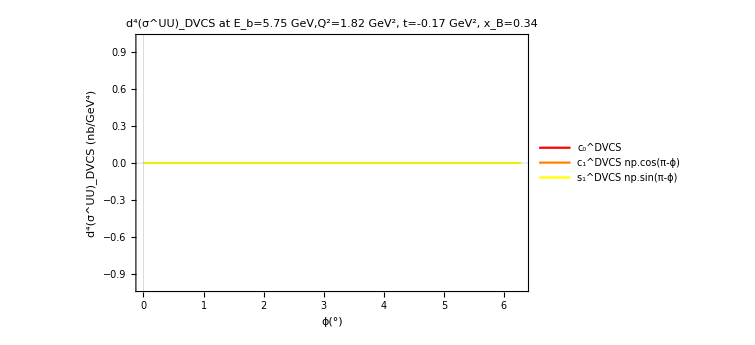

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[
cODVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]+cODVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
],
ConvertGeVMinus6ToNbGevMinus4[
(c1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+c1DVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Cos[1(π-ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
(s1DVCS[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]+s1DVCS[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]])Sin[1(π- ϕ)]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"c_0^DVCS",
"c_1^DVCS np.cos(π-ϕ)",
"s_1^DVCS np.sin(π-ϕ)"
}
],
{0.85,0.75}
],
PlotStyle->{Red, Orange, Yellow},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS (nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific",
PlotRange->All
]
```

#### (#4.3.1.2): DVCS σ^LU | Unpolarized Beam, Longitudinally-Polarized Target

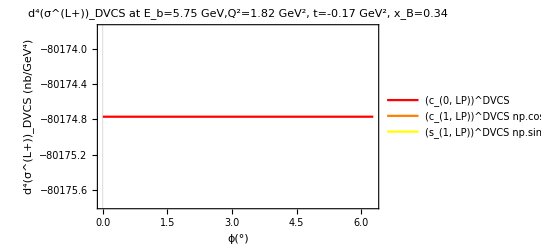

```mathematica
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[
cODVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,ℋ,ℋT,ℰ,ℰT,Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT],EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],EffectiveFormFactor[ξ,Conjugate[ℋ]],EffectiveFormFactor[ξ,Conjugate[ℋT]],EffectiveFormFactor[ξ,Conjugate[ℰ]],EffectiveFormFactor[ξ,Conjugate[ℰT]]]
],
ConvertGeVMinus6ToNbGevMinus4[
c1DVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Cos[1(π-ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
s1DVCS[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,K,F1,F2,EffectiveFormFactor[ξ,ℋ],EffectiveFormFactor[ξ,ℋT],EffectiveFormFactor[ξ,ℰ],EffectiveFormFactor[ξ,ℰT],Conjugate[ℋ],Conjugate[ℋT],Conjugate[ℰ],Conjugate[ℰT]]Sin[1(π- ϕ)]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"(c_(0, LP))^DVCS",
"(c_(1, LP))^DVCS np.cos(π-ϕ)",
"(s_(1, LP))^DVCS np.sin(π-ϕ)"
}
],
{0.85,0.75}
],
PlotStyle->{Red, Orange, Yellow},
FrameLabel->{"ϕ(°)","d^4(σ^(L+))_DVCS (nb/GeV^4)"},
PlotLabel->"d^4(σ^(L+))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotTheme->"Scientific",
PlotRange->All
]
```

## (#4.3): Interference:

### (#4.3.1): Propagator 1, 𝒫_1(ϕ):

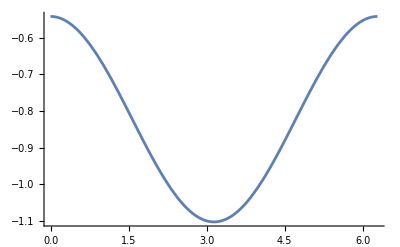

```mathematica
Propagator1[qSquared_,xB_,t_,ϕ_,ϵ_,y_,K_]:=(qSquared+2(((-qSquared)/(2y(1+ϵ^2)))(1+2 K Cos[π-ϕ]-(t/qSquared)(1-xB(2-y)+(y ϵ^2)/2)+(y ϵ^2)/2)))/qSquared;

Plot[Propagator1[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

### (#4.3.2): Propagator 2, 𝒫_2(ϕ):

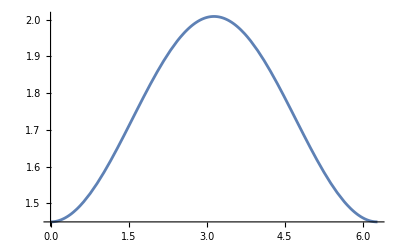

```mathematica
Propagator2[qSquared_,xB_,t_,ϕ_,ϵ_,y_,K_]:=(-2(((-qSquared)/(2y(1+ϵ^2)))(1+2 K Cos[π-ϕ]-(t/qSquared)(1-xB(2-y)+(y ϵ^2)/2)+(y ϵ^2)/2))+t)/qSquared;

Plot[Propagator2[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

### (#4.3.3): Interference Contribution, ℐ:

#### (#4.3.3.1): Interference Contribution Function:

```mathematica
InterferenceContribution[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=
(1/(xB t y^3 Propagator1[qSquared,xB,t,ϕ,ϵ,y,K]Propagator2[qSquared,xB,t,ϕ,ϵ,y,K]))*(
cOI[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]+
c1I[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]+
c2I[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π-ϕ)]+
c3I[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ]Cos[3(π-ϕ)]+
s1I[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π-ϕ)]+
s2I[WWSetting,λ,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π-ϕ)]+
s3I[WWSetting,Λ,qSquared,xB,t,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π-ϕ)]) ;
```

#### (#4.3.3.2): Plot of Propagator 1, 𝒫_1(ϕ):

```mathematica
(* Here is a plot of the first Lepton Propagator *)
Plot[Propagator1[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

-Graphics-

#### (#4.3.3.3): Plot of Propagator 2, 𝒫_2(ϕ):

```mathematica
(* Here is a plot of the second Lepton Propagator *)
Plot[Propagator2[qSquared,xB,t,ϕ,ϵ,y,K],{ϕ,0,2π}]
```

-Graphics-

#### (#4.3.3.4): ℐ σ^UU | Unpolarized Beam, Unpolarized Target:

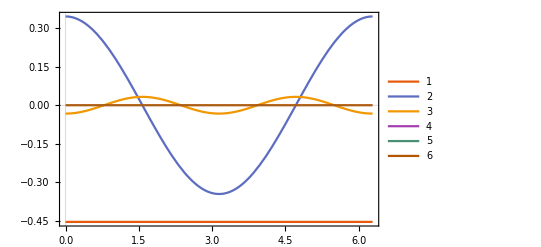

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the *unpolarized* Lepton Helicity beam*)
Plot[
{
(1/2)(cOI[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
(1/2)(c1I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]+c1I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]),
(1/2)(c2I[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π- ϕ)]+c2I[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π- ϕ)]),
(1/2)(s1I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π- ϕ)]+s1I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π- ϕ)]),
(1/2)(s2I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π- ϕ)]+s2I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π- ϕ)]),
(1/2)(s3I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π- ϕ)]+s3I[WWOn,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π- ϕ)])
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific",
PlotRange->All]
```

#### (#4.3.3.5): ℐ σ^(U+) | (+) Helicity Beam and Unpolarized Target:

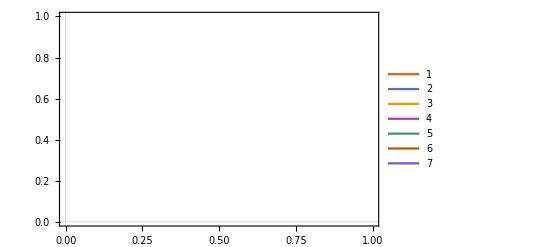

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (+) Lepton Helicity beam*)
Plot[{
cOI[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
c1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ],
c2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ],
c3I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]Cos[π-3ϕ],
s1I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ],
s2I[LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ],
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotRange->All,
PlotTheme->"Scientific"]
```

#### (#4.3.3.6): ℐ σ^(U-) | (-) Helicity Beam, Unpolarized Target:

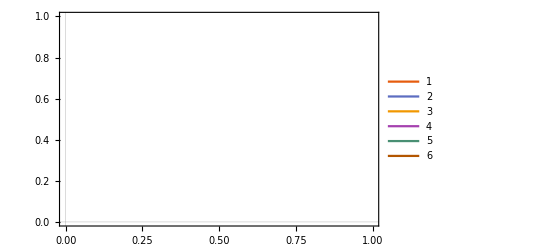

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (-) Lepton Helicity beam*)
Plot[{
cOI[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
c1I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-1 ϕ],
c2I[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[π-2ϕ],
s1I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-1 ϕ],
s2I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-2ϕ],
s3I[unpolarizedTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[π-3ϕ]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotTheme->"Scientific"]
```

#### (#4.3.3.7): ℐ σ^LU | Unpolarized Beam, LP Target:

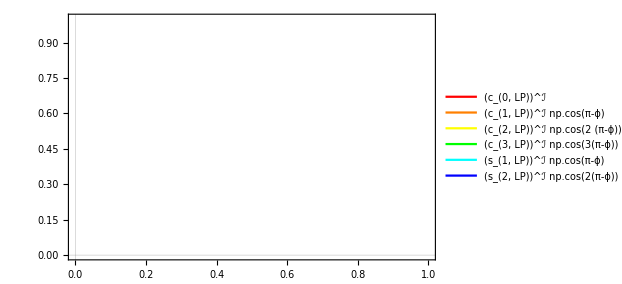

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the *unpolarized* Lepton Helicity beam*)
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[(1/2)(cOI[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[(1/2)(c1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])Cos[1(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[(1/2)(c2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])Cos[2(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
(1/2)(s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])Sin[1(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
(1/2)(s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])Sin[2(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
(1/2)(s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])Sin[3(π- ϕ)]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"(c_(0, LP))^ℐ",
"(c_(1, LP))^ℐ np.cos(π-ϕ)",
"(c_(2, LP))^ℐ np.cos(2 (π-ϕ))",
"(c_(3, LP))^ℐ np.cos(3(π-ϕ))",
"(s_(1, LP))^ℐ np.cos(π-ϕ)",
"(s_(2, LP))^ℐ np.cos(2(π-ϕ))",
"(s_(3, LP))^ℐ np.sin(3(π-ϕ))"
}
],
{0.85,0.75}
],
PlotStyle->{Red, Orange, Yellow, Green, Cyan, Blue, Purple},
PlotTheme->"Scientific",
PlotRange->All]
```

#### (#4.3.3.8): ℐ σ^(L+) | (+) Helicity Beam, LP Target:

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (+) Lepton Helicity beam*)
Plot[{
ConvertGeVMinus6ToNbGevMinus4[cOI[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]],
ConvertGeVMinus6ToNbGevMinus4[c1I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π-ϕ)]],
ConvertGeVMinus6ToNbGevMinus4[c2I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π-ϕ)]],
ConvertGeVMinus6ToNbGevMinus4[c3I[LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ]Cos[3(π-ϕ)]],
ConvertGeVMinus6ToNbGevMinus4[s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π-ϕ)]],
ConvertGeVMinus6ToNbGevMinus4[s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π-ϕ)]],
ConvertGeVMinus6ToNbGevMinus4[s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π-ϕ)]]
},
{ϕ,0,2π},
PlotLegends->Automatic,
PlotRange->All,
PlotTheme->"Scientific"]
```

-Graphics-

#### (#4.3.3.9): ℐ σ^(L-) | (-) Helicity Beam, LP Target:

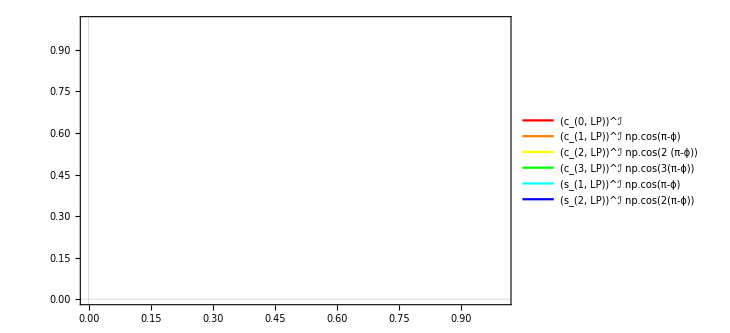

```mathematica
(* Here is the plot of every contributing Subscript[c, n]^ℐ in the (-) Lepton Helicity beam*)
Plot[
{
ConvertGeVMinus6ToNbGevMinus4[
cOI[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[c1I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[1(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[c2I[LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Cos[2(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
s1I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[1(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
s2I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[2(π- ϕ)]
],
ConvertGeVMinus6ToNbGevMinus4[
s3I[lpTargetΛ,qSquared,xB,t,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]Sin[3(π- ϕ)]
]
},
{ϕ,0,2π},
PlotLegends->Placed[
LineLegend[
{
"(c_(0, LP))^ℐ",
"(c_(1, LP))^ℐ np.cos(π-ϕ)",
"(c_(2, LP))^ℐ np.cos(2 (π-ϕ))",
"(c_(3, LP))^ℐ np.cos(3(π-ϕ))",
"(s_(1, LP))^ℐ np.cos(π-ϕ)",
"(s_(2, LP))^ℐ np.cos(2(π-ϕ))",
"(s_(3, LP))^ℐ np.sin(3(π-ϕ))"
}
],
{0.85,0.75}
],
PlotStyle->{Red, Orange, Yellow, Green, Cyan, Blue, Purple},
PlotTheme->"Scientific",
PlotRange->All]
```

## (#5): Total Cross Section: σ^XY | X = beam polarization, Y = target polarization

## (#5.1): Total Cross Section Function:

```mathematica
BKM10CrossSection[WWSetting_,λ_,Λ_,qSquared_,xB_,t_,ϕ_,ϵ_,y_,ξ_,tPrime_,K_,KTilde_,F1_,F2_,ℋ_,ℋT_,ℰ_,ℰT_]:=
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))(0 *BHContribution[WWSetting]+DVCSContribution[WWSetting,λ,Λ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWSetting,λ,Λ,qSquared,xB,t,ϕ,ϵ,y,ξ,tPrime,K,KTilde,F1,F2,ℋ,ℋT,ℰ,ℰT])
];
```

## (#6): Plots of the Cross Section:

## (#4.4.1): σ^UU | Unpolarized Beam, Unpolarized Target

### (#4.4.1.1): σ^UU | Unpolarized Beam, Unpolarized Target

#### (#4.4.1.1.1): Pure DVCS | σ^UU

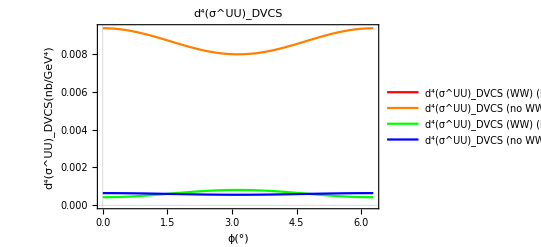

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))1/2*(DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))1/2*(DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^UU)_DVCS (WW) (kinematic bin 1)",
"d^4(σ^UU)_DVCS (no WW) (kinematic bin 1)",
"d^4(σ^UU)_DVCS (WW) (kinematic bin 2)",
"d^4(σ^UU)_DVCS (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_DVCS",
PlotTheme->"Scientific"
]
```

#### (#4.4.1.1.2): Pure Interference | σ^UU

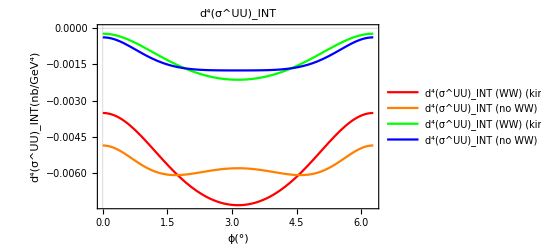

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^UU)_INT (WW) (kinematic bin 1)",
"d^4(σ^UU)_INT (no WW) (kinematic bin 1)",
"d^4(σ^UU)_INT (WW) (kinematic bin 2)",
"d^4(σ^UU)_INT (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange,Green,Blue},
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^UU)_INT",
PlotTheme->"Scientific"
]
```

#### (#4.4.1.1.3): Total Cross Section | σ^UU

```mathematica
Plot[{
1/2(BKM10CrossSection[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
1/2(BKM10CrossSection[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
1/2(BKM10CrossSection[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]),
1/2(BKM10CrossSection[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
},
{ϕ,0,2π},
PlotLegends->{
"Total d^4σ w/o BH (WW) (kinematic bin 1)",
"Total d^4σ w/o BH (no WW) (kinematic bin 1)",
"Total d^4σ w/o BH (WW) (kinematic bin 2)",
"Total d^4σ w/o BH (no WW) (kinematic bin 2)"
},
PlotRange->All,
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4σ^UU(nb/GeV^4)"},
PlotLabel->"d^4σ^UU",
PlotTheme->"Scientific"
]
```

$Aborted

## (#4.4.2): σ^LU | Polarized Beam, Unpolarized Target

### (#4.4.2.1): σ^(+U) | (+) Polarized Beam, Unpolarized Target

#### (#4.4.2.1.1): Pure DVCS | σ^(+U)

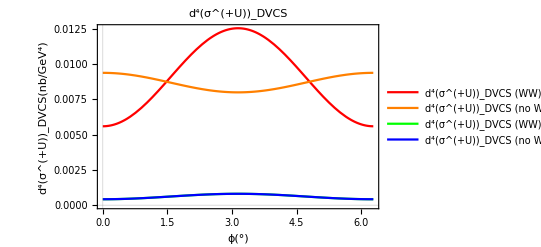

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^(+U))_DVCS (WW) (kinematic bin 1)",
"d^4(σ^(+U))_DVCS (no WW) (kinematic bin 1)",
"d^4(σ^(+U))_DVCS (WW) (kinematic bin 2)",
"d^4(σ^(+U))_DVCS (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4(σ^(+U))_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^(+U))_DVCS",
PlotTheme->"Scientific"
]
```

#### (#4.4.2.1.2): Pure Interference | σ^(+U)

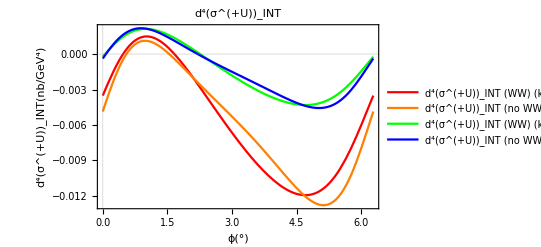

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^(+U))_INT (WW) (kinematic bin 1)",
"d^4(σ^(+U))_INT (no WW) (kinematic bin 1)",
"d^4(σ^(+U))_INT (WW) (kinematic bin 2)",
"d^4(σ^(+U))_INT (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange,Green,Blue},
FrameLabel->{"ϕ(°)","d^4(σ^(+U))_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^(+U))_INT",
PlotTheme->"Scientific"
]
```

#### (#4.4.2.1.3): Total Cross Section | σ^(+U)

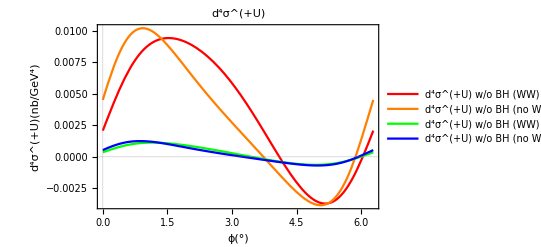

```mathematica
Plot[{
BKM10CrossSection[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
},
{ϕ,0,2π},
PlotLegends->{
"d^4σ^(+U) w/o BH (WW) (kinematic bin 1)",
"d^4σ^(+U) w/o BH (no WW) (kinematic bin 1)",
"d^4σ^(+U) w/o BH (WW) (kinematic bin 2)",
"d^4σ^(+U) w/o BH (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4σ^(+U)(nb/GeV^4)"},
PlotLabel->"d^4σ^(+U)",
PlotTheme->"Scientific"
]
```

### (#4.4.2.2): σ^-U | (-) Polarized Beam, Unpolarized Target

#### (#4.4.2.2.1): Pure DVCS | σ^-U

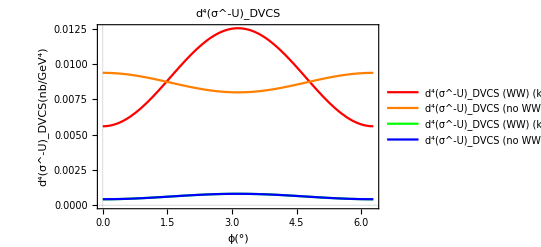

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^-U)_DVCS (WW) (kinematic bin 1)",
"d^4(σ^-U)_DVCS (no WW) (kinematic bin 1)",
"d^4(σ^-U)_DVCS (WW) (kinematic bin 2)",
"d^4(σ^-U)_DVCS (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4(σ^-U)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^-U)_DVCS",
PlotTheme->"Scientific"
]
```

#### (#4.4.2.2.2): Pure Interference | σ^-U

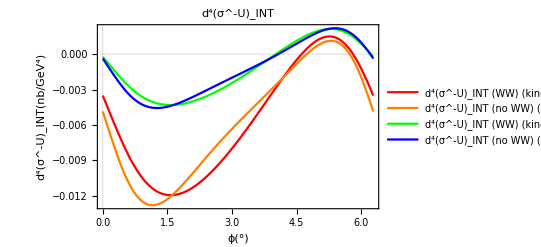

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^-U)_INT (WW) (kinematic bin 1)",
"d^4(σ^-U)_INT (no WW) (kinematic bin 1)",
"d^4(σ^-U)_INT (WW) (kinematic bin 2)",
"d^4(σ^-U)_INT (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange,Green,Blue},
FrameLabel->{"ϕ(°)","d^4(σ^-U)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^-U)_INT",
PlotTheme->"Scientific"
]
```

#### (#4.4.2.2.3): Total Cross Section | σ^-U

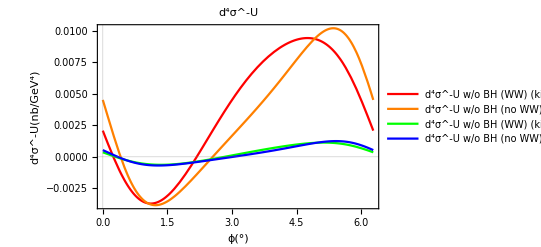

```mathematica
Plot[{
BKM10CrossSection[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
},
{ϕ,0,2π},
PlotLegends->{
"d^4σ^-U w/o BH (WW) (kinematic bin 1)",
"d^4σ^-U w/o BH (no WW) (kinematic bin 1)",
"d^4σ^-U w/o BH (WW) (kinematic bin 2)",
"d^4σ^-U w/o BH (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4σ^-U(nb/GeV^4)"},
PlotLabel->"d^4σ^-U",
PlotTheme->"Scientific"
]
```

## (#4.4.3): σ^UL | Unpolarized Beam, Polarized Target

### (#4.4.3.1): σ^UL | Unpolarized Beam, Longitudinally-Polarized Target

#### (#4.4.3.1.1): Pure DVCS | σ^UL

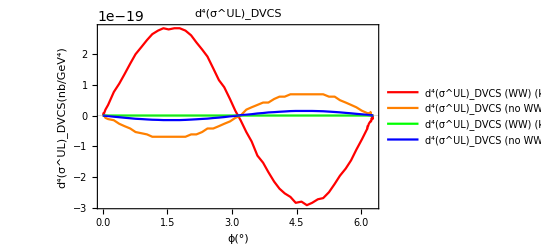

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2(DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,
qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2(DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2(DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,
qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2(DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,
qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^UL)_DVCS (WW) (kinematic bin 1)",
"d^4(σ^UL)_DVCS (no WW) (kinematic bin 1)",
"d^4(σ^UL)_DVCS (WW) (kinematic bin 2)",
"d^4(σ^UL)_DVCS (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4(σ^UL)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^UL)_DVCS",
PlotTheme->"Scientific"
]
```

#### (#4.4.3.1.2): Pure Interference | σ^UL

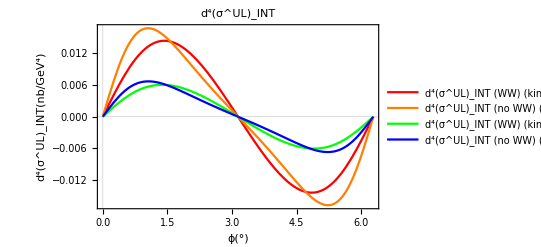

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^UL)_INT (WW) (kinematic bin 1)",
"d^4(σ^UL)_INT (no WW) (kinematic bin 1)",
"d^4(σ^UL)_INT (WW) (kinematic bin 2)",
"d^4(σ^UL)_INT (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange,Green,Blue},
FrameLabel->{"ϕ(°)","d^4(σ^UL)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^UL)_INT",
PlotTheme->"Scientific"
]
```

#### (#4.4.3.3.1): Total Cross Section | σ^UL

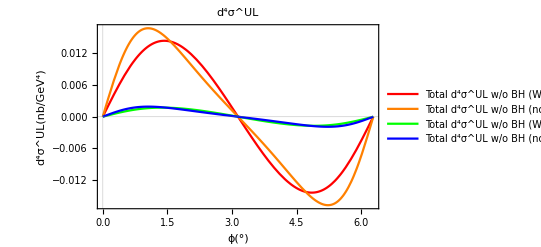

```mathematica
Plot[{
1/2(BKM10CrossSection[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
1/2(BKM10CrossSection[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]),
1/2(BKM10CrossSection[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]),
1/2(BKM10CrossSection[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+BKM10CrossSection[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
},
{ϕ,0,2π},
PlotLegends->{
"Total d^4σ^UL w/o BH (WW) (kinematic bin 1)",
"Total d^4σ^UL w/o BH (no WW) (kinematic bin 1)",
"Total d^4σ^UL w/o BH (WW) (kinematic bin 2)",
"Total d^4σ^UL w/o BH (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4σ^UL(nb/GeV^4)"},
PlotLabel->"d^4σ^UL",
PlotTheme->"Scientific"
]
```

## (#4.4.4): σ^LL | Polarized Beam, Polarized Target

### (#4.4.4.1): σ^(+L) | Polarized Target, (+) Polarized Beam

#### (#4.4.4.1.1): Pure DVCS | σ^(+L)

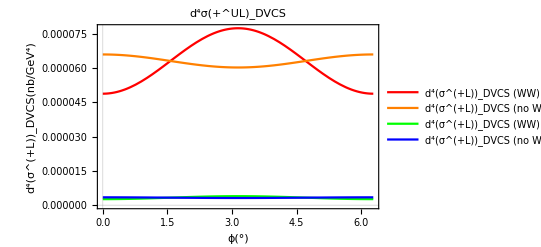

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^(+L))_DVCS (WW) (kinematic bin 1)",
"d^4(σ^(+L))_DVCS (no WW) (kinematic bin 1)",
"d^4(σ^(+L))_DVCS (WW) (kinematic bin 2)",
"d^4(σ^(+L))_DVCS (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_DVCS(nb/GeV^4)"},
PlotLabel->"d^4σ(+^UL)_DVCS",
PlotTheme->"Scientific"
]
```

#### (#4.4.4.1.2): Pure Interference | σ^(L+)

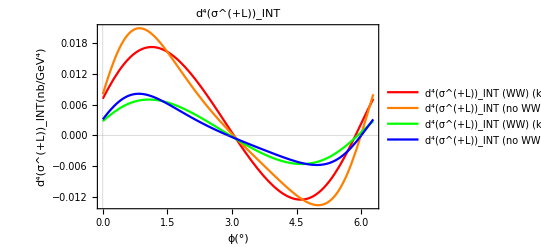

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^(+L))_INT (WW) (kinematic bin 1)",
"d^4(σ^(+L))_INT (no WW) (kinematic bin 1)",
"d^4(σ^(+L))_INT (WW) (kinematic bin 2)",
"d^4(σ^(+L))_INT (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange,Green,Blue},
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^(+L))_INT",
PlotTheme->"Scientific"
]
```

#### (#4.4.4.1.3): Combined | σ^(L+)

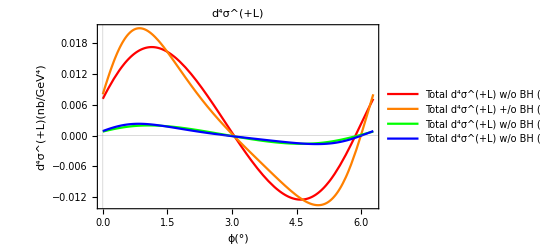

```mathematica
Plot[{
BKM10CrossSection[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
},
{ϕ,0,2π},
PlotLegends->{
"Total d^4σ^(+L) w/o BH (WW) (kinematic bin 1)",
"Total d^4σ^(+L) +/o BH (no WW) (kinematic bin 1)",
"Total d^4σ^(+L) w/o BH (WW) (kinematic bin 2)",
"Total d^4σ^(+L) w/o BH (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4σ^(+L)(nb/GeV^4)"},
PlotLabel->"d^4σ^(+L)",
PlotTheme->"Scientific"
]
```

### (#4.4.4.2): σ^(L-) | Polarized Target, (-) Polarized Beam

#### (#4.4.4.2.1): Pure DVCS | σ^(L-)

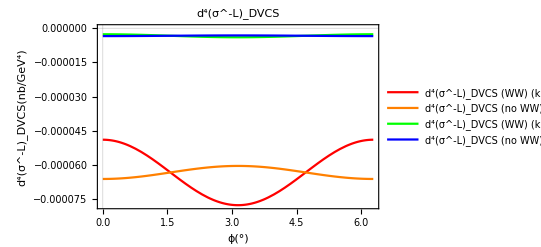

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^-L)_DVCS (WW) (kinematic bin 1)",
"d^4(σ^-L)_DVCS (no WW) (kinematic bin 1)",
"d^4(σ^-L)_DVCS (WW) (kinematic bin 2)",
"d^4(σ^-L)_DVCS (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4(σ^-L)_DVCS(nb/GeV^4)"},
PlotLabel->"d^4(σ^-L)_DVCS",
PlotTheme->"Scientific"
]
```

#### (#4.4.4.2.2): Pure Interference | σ^(L-)

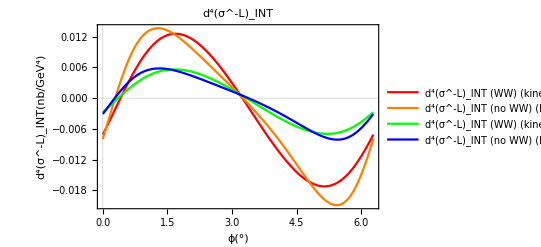

```mathematica
Plot[{
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
],
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]},
{ϕ,0,2π},
PlotLegends->{
"d^4(σ^-L)_INT (WW) (kinematic bin 1)",
"d^4(σ^-L)_INT (no WW) (kinematic bin 1)",
"d^4(σ^-L)_INT (WW) (kinematic bin 2)",
"d^4(σ^-L)_INT (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange,Green,Blue},
FrameLabel->{"ϕ(°)","d^4(σ^-L)_INT(nb/GeV^4)"},
PlotLabel->"d^4(σ^-L)_INT",
PlotTheme->"Scientific"
]
```

#### (#4.4.4.2.3): Total Cross Section | σ^(L-)

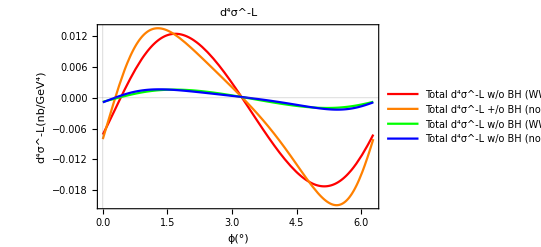

```mathematica
Plot[{
BKM10CrossSection[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT],
BKM10CrossSection[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
},
{ϕ,0,2π},
PlotLegends->{
"Total d^4σ^-L w/o BH (WW) (kinematic bin 1)",
"Total d^4σ^-L +/o BH (no WW) (kinematic bin 1)",
"Total d^4σ^-L w/o BH (WW) (kinematic bin 2)",
"Total d^4σ^-L w/o BH (no WW) (kinematic bin 2)"
},
PlotStyle->{Red, Orange, Green, Blue},
FrameLabel->{"ϕ(°)","d^4σ^-L(nb/GeV^4)"},
PlotLabel->"d^4σ^-L",
PlotTheme->"Scientific"
]
```

## (#7): Exporting CSV Data Files:

## (#7.1): Pure DVCS:

### (#7.1.1): Kinematic Bin 1 | Unpolarized Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_unpolarized_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.2): Kinematic Bin 1 | Unpolarized Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.3): Kinematic Bin 2 | Unpolarized Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_unpolarized_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))1/2*(DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.4): Kinematic Bin 2 | Unpolarized Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))1/2*(DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"]
```

jd_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_2_v3.csv

```mathematica
"jd_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_2_v3.csv"
```

jd_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_2_v3.csv

### (#7.1.5): Kinematic Bin 1 | (+) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_plus_beam_unpolarized_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.6): Kinematic Bin 1 | (+) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_plus_beam_unpolarized_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.7): Kinematic Bin 2 | (+) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_plus_beam_unpolarized_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.8): Kinematic Bin 2 | (+) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_plus_beam_unpolarized_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.9): Kinematic Bin 1 | (-) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_minus_beam_unpolarized_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.10): Kinematic Bin 1 | (-) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_minus_beam_unpolarized_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.11): Kinematic Bin 2 | (-) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_minus_beam_unpolarized_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.12): Kinematic Bin 2 | (-) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_minus_beam_unpolarized_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))DVCSContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.13): Kinematic Bin 1 | Unpolarized Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_lp_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.14): Kinematic Bin 1 | Unpolarized Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))1/2*(DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.15): Kinematic Bin 2 | Unpolarized Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_lp_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))1/2*(DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.16): Kinematic Bin 2 | Unpolarized Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 yFutureKinematics^2 xBFutureKinematics)/(8 π qSquaredFutureKinematics^2 √(1+ϵFutureKinematics^2)))1/2*(DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"]
```

jd_dvcs_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv

```mathematica
"jd_dvcs_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv"
```

jd_dvcs_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv

### (#7.1.17): Kinematic Bin 1 | (+) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_plus_beam_lp_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.18): Kinematic Bin 1 | (+) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_plus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.19): Kinematic Bin 2 | (+) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_plus_beam_lp_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.20): Kinematic Bin 2 | (+) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_plus_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.21): Kinematic Bin 1 | (-) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_minus_beam_lp_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.22): Kinematic Bin 1 | (-) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_minus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,K,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.23): Kinematic Bin 2 | (-) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_dvcs_minus_beam_lp_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.1.24): Kinematic Bin 2 | (-) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_dvcs_minus_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
Re[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))DVCSContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,KFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

## (#7.2): Pure Interference:

### (#7.2.1): Kinematic Bin 1 | Unpolarized Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_interference_unpolarized_beam_unpolarized_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.2): Kinematic Bin 1 | Unpolarized Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_interference_unpolarized_beam_unpolarized_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.3): Kinematic Bin 2 | Unpolarized Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_interference_unpolarized_beam_unpolarized_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.4): Kinematic Bin 2 | Unpolarized Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_interference_unpolarized_beam_unpolarized_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.5): Kinematic Bin 1 | (+) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_interference_plus_beam_unpolarized_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.6): Kinematic Bin 1 | (+) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_interference_plus_beam_unpolarized_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.7): Kinematic Bin 2 | (+) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_interference_plus_beam_unpolarized_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.8): Kinematic Bin 2 | (+) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_interference_plus_beam_unpolarized_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.9): Kinematic Bin 1 | (-) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_interference_minus_beam_unpolarized_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.10): Kinematic Bin 1 | (-) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_interference_minus_beam_unpolarized_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.11): Kinematic Bin 2 | (-) Beam | Unpolarized Target | WW Relations On:

```mathematica
Export[
"jd_interference_minus_beam_unpolarized_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.12): Kinematic Bin 2 | (-) Beam | Unpolarized Target | WW Relations Off:

```mathematica
Export[
"jd_interference_minus_beam_unpolarized_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,unpolarizedTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.13): Kinematic Bin 1 | Unpolarized Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_interference_unpolarized_beam_lp_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.14): Kinematic Bin 1 | Unpolarized Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_interference_unpolarized_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.15): Kinematic Bin 2 | Unpolarized Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_interference_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.16): Kinematic Bin 2 | Unpolarized Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_interference_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
1/2(InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]+InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT])
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.17): Kinematic Bin 1 | (+) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_interference_plus_beam_lp_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.18): Kinematic Bin 1 | (+) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_interference_plus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.19): Kinematic Bin 2 | (+) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_interference_plus_beam_lp_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.20): Kinematic Bin 2 | (+) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_interference_plus_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλPlus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.21): Kinematic Bin 1 | (-) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_interference_minus_beam_lp_target_ww_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.22): Kinematic Bin 1 | (-) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_interference_minus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquared,xB,t,ϕ,ϵ,y,ξ,tP,K,kT,F1,F2,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.23): Kinematic Bin 2 | (-) Beam | LP Target | WW Relations On:

```mathematica
Export[
"jd_interference_minus_beam_lp_target_ww_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOn,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

### (#7.2.24): Kinematic Bin 2 | (-) Beam | LP Target | WW Relations Off:

```mathematica
Export[
"jd_interference_minus_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
QuantityMagnitude[
ConvertGeVMinus6ToNbGevMinus4[
((ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2)))
InterferenceContribution[WWOff,LeptonλMinus,lpTargetΛ,qSquaredFutureKinematics,xBFutureKinematics,tFutureKinematics,ϕ,ϵFutureKinematics,yFutureKinematics,ξFutureKinematics,tPFutureKinematics,KFutureKinematics,kTFutureKinematics,F1FutureKinematics,F2FutureKinematics,ℋ,ℋT,ℰ,ℰT]
]
],
{ϕ,0,2π, (2π)/360}],
"CSV"];
```

## (#7.3): Total Cross Section

## (#X): Testing:

## (#X.1): Cross-Checking c_2^ℐ:

Define the variables in question.

```mathematica
cpp=0.002414077755645961;
c0p=-0.21172805503862407;
curlyCpp=-57.8406742181105;
curlyC0p=1.9568253283721;
```

Try the individual product:

```mathematica
cpp*curlyCpp
c0p*curlyC0p
```

-0.139632

-0.414315

So the sum must be:

```mathematica
cpp*curlyCpp+c0p*curlyC0p
```

-0.553947

In conclusion, the Mathematica function is probably getting the wrong arguments.

## (#X.2): Cross-Checking s_2^ℐ:

First of all, Python is probably correct here...

The individual pieces are:

```mathematica
spp=0.004810462931411953;
s0p=0.5860907929841134;
curlySpp=-20.177953752886854;
curlyS0p=0.729452642853709;
```

Individual products are:

```mathematica
spp*curlySpp
s0p*curlyS0p
```

-0.0970653

0.427525

The sum is:

```mathematica
spp*curlySpp+s0p*curlyS0p
```

0.33046

Python gives 0.3304601793344807.

There is also one more possibility:

```mathematica
(0.004810462931411953*-20.177953752886854)+(0.5860907929841134*0.729452642853709)
```

0.33046

## (#X.3): Testing Amplitude Squared Prefactor:

```mathematica
(ElectromagneticFineStructureConstant^3 y^2 xB)/(8 π qSquared^2 √(1+ϵ^2))
```

3.53095×10^-10 /GeV^4

## (#X.4): Understanding “Associations” in Mathematica:

```mathematica
(*Step 1:Define the functions and their arguments*)
functions=<|
"(C^unp)_(++)(n=0)"->CunpPP0,
"(C^unp)_(++)(n=1)"->CunpPP1,
"(C^unp)_(++)(n=2)"->CunpPP2,
"(C^unp)_(++)(n=3)"->CunpPP3,
"(C^(unp, V))_(++)(n=0)"->CunpVPP0,
"(C^(unp, V))_(++)(n=1)"->CunpVPP1,
"(C^(unp, V))_(++)(n=2)"->CunpVPP2,
"(C^(unp, V))_(++)(n=3)"->CunpVPP3,
"(C^(unp, A))_(++)(n=0)"->CunpAPP0,
"(C^(unp, A))_(++)(n=1)"->CunpAPP1,
"(C^(unp, A))_(++)(n=2)"->CunpAPP2,
"(C^(unp, A))_(++)(n=3)"->CunpAPP3,
"(C^unp)_(0+)(n=0)"->Cunp0P0,
"(C^unp)_(0+)(n=1)"->Cunp0P1,
"(C^unp)_(0+)(n=2)"->Cunp0P2,
"(C^(unp, V))_(0+)(n=0)"->Cunp0P0V,
"(C^(unp, V))_(0+)(n=1)"->Cunp0P1V,
"(C^(unp, V))_(0+)(n=2)"->Cunp0P2V,
"(C^(unp, A))_(0+)(n=0)"->Cunp0P0A,
"(C^(unp, A))_(0+)(n=1)"->Cunp0P1A,
"(C^(unp, A))_(0+)(n=2)"->Cunp0P2A
|>;
```

```mathematica
arguments=<|
"(C^unp)_(++)(n=0)"->{qSquared,xB,t,ϵ,y,kT},
"(C^unp)_(++)(n=1)"->{qSquared,xB,t,ϵ,y,K},
"(C^unp)_(++)(n=2)"->{qSquared,xB,t,ϵ,y,tP,kT},
"(C^unp)_(++)(n=3)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, V))_(++)(n=0)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, V))_(++)(n=1)"->{qSquared,xB,t,ϵ,y,tP,K},
"(C^(unp, V))_(++)(n=2)"->{qSquared,xB,t,ϵ,y,tP,kT},
"(C^(unp, V))_(++)(n=3)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, A))_(++)(n=0)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, A))_(++)(n=1)"->{qSquared,xB,t,ϵ,y,tP,K},
"(C^(unp, A))_(++)(n=2)"->{qSquared,xB,t,ϵ,y,tP,kT},
"(C^(unp, A))_(++)(n=3)"->{qSquared,xB,t,ϵ,y,tP,K},
"(C^unp)_(0+)(n=0)"->{qSquared,xB,t,ϵ,y,K},
"(C^unp)_(0+)(n=1)"->{qSquared,xB,t,ϵ,y,tP},
"(C^unp)_(0+)(n=2)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, V))_(0+)(n=0)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, V))_(0+)(n=1)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, V))_(0+)(n=2)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, A))_(0+)(n=0)"->{qSquared,xB,t,ϵ,y,K},
"(C^(unp, A))_(0+)(n=1)"->{qSquared,xB,t,ϵ,y,kT},
"(C^(unp, A))_(0+)(n=2)"->{qSquared,xB,t,ϵ,y,tP,K}
|>;
```

```mathematica
(*Step 2:Evaluate each function with its corresponding arguments*)
results=Table[
functions[key]@@arguments[key],
{key,Keys[functions]}
];
```

```mathematica
(*Step 3:Create labels for each function*)
labels=Keys[functions]
```

{(C^unp)_(++)(n=0),(C^unp)_(++)(n=1),(C^unp)_(++)(n=2),(C^unp)_(++)(n=3),(C^(unp, V))_(++)(n=0),(C^(unp, V))_(++)(n=1),(C^(unp, V))_(++)(n=2),(C^(unp, V))_(++)(n=3),(C^(unp, A))_(++)(n=0),(C^(unp, A))_(++)(n=1),(C^(unp, A))_(++)(n=2),(C^(unp, A))_(++)(n=3),(C^unp)_(0+)(n=0),(C^unp)_(0+)(n=1),(C^unp)_(0+)(n=2),(C^(unp, V))_(0+)(n=0),(C^(unp, V))_(0+)(n=1),(C^(unp, V))_(0+)(n=2),(C^(unp, A))_(0+)(n=0),(C^(unp, A))_(0+)(n=1),(C^(unp, A))_(0+)(n=2)}

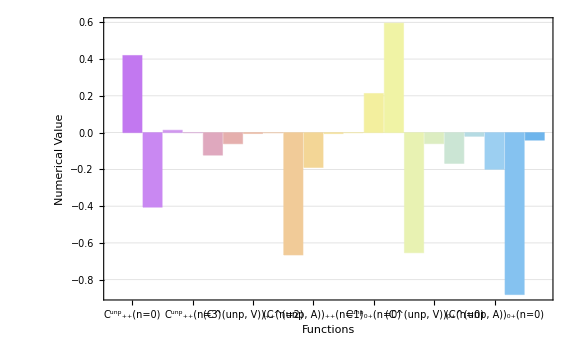

```mathematica
(*Step 4:Generate the bar chart*)
BarChart[
results,
ChartLabels->labels,
BarSpacing->0.05,
PlotTheme->"Detailed",
ChartStyle->"Pastel",
LabelStyle->Directive[Bold,FontSize->6],
RotateLabel->True,
FrameTicks->{{Automatic,None},{Automatic,None}},
Frame->True,
AxesOrigin->{0,0},
FrameLabel->{"Functions","Numerical Value"},
ImageSize->Large
]
```